```mathematica
D[realkl[4,0],θ]
```

(3 (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ]))/(16 √π)

```mathematica
Integrate[HeavisideTheta[θ-Pi/2]*SphericalHarmonicY[1,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

0

## Formulation

```mathematica
realkl[k_,l_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,θ,0],l==0}}]
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0},{(√2)*ComplexExpand[Im[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l<0}}]
```

```mathematica
Clear[η,t,ϕ,ϕ1,ϕ2,ϕ3, η1, η2, η3,We]
```

```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+1/r^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) ϕ^(0,0,1,0)[r,θ,φ,t]+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) ϕ^(0,1,0,0)[r,θ,φ,t])/r^2-ϕ^(1,0,0,0)[r,θ,φ,t]

```mathematica
(*the potential phi has two subscripts. first subscript=1 is inner fluid, =2 is outer fluid.*)
```

```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];(*drop*)
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];(*outer fluid*)
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
nhat={1,-e/r D[η[θ,φ,t],θ],-e/(r*Sin[θ])D[η[θ,φ,t],φ]}/(√(1+(-e/r D[η[θ,φ,t],θ])^2+(e/(r*Sin[θ])D[η[θ,φ,t],φ])^2));
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ2[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+1/r^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t])+1/r^2(e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])-e ϕ21^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ23^(1,0,0,0)[r,θ,φ,t]

```mathematica
nopen=(Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"]-Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"]).nhat
```

-((e Csc[θ] (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (1/r Csc[θ] (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t])-1/r Csc[θ] (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t])))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2)))-(e (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) ((e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])/r-(e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))+(e ϕ11^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]-e ϕ21^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ23^(1,0,0,0)[r,θ,φ,t])/(√(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))

```mathematica
curvature=2-2 η[θ,φ,t]-2 η[θ,φ,t]^3-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-3 Csc[θ]^2 η[θ,φ,t]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-3 Cot[θ] η[θ,φ,t]^2 Derivative[1,0,0][η][θ,φ,t]+Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t]-3 η[θ,φ,t]^2 Derivative[2,0,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]+2 (η[θ,φ,t]^2+Csc[θ]^2 η[θ,φ,t] Derivative[0,2,0][η][θ,φ,t]+Cot[θ] η[θ,φ,t] Derivative[1,0,0][η][θ,φ,t]+η[θ,φ,t] Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
Clear[ρ1,ρ2,We];
normalst=(-ρ1*(D[ϕ1[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ1[r,θ,φ,t],φ]^2)/r^2+D[ϕ1[r,θ,φ,t],θ]^2/r^2+D[ϕ1[r,θ,φ,t],r]^2))+ρ2*(D[ϕ2[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ2[r,θ,φ,t],φ]^2)/r^2+D[ϕ2[r,θ,φ,t],θ]^2/r^2+D[ϕ2[r,θ,φ,t],r]^2)))-1/We*(curvature);(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ23^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
nopenstpertr1=Series[nopen/.r->1+η[θ,φ,t],{e,0,3}]//Normal
```

e (ϕ11^(1,0,0,0)[1,θ,φ,t]-ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (ϕ12^(1,0,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (-Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])-η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])+ϕ13^(1,0,0,0)[1,θ,φ,t]-ϕ23^(1,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We-ρ1 ϕ11^(0,0,0,1)[1,θ,φ,t]+ρ2 ϕ21^(0,0,0,1)[1,θ,φ,t])+e^2 (1/We(2 η2[θ,φ,t]+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] η1^(0,2,0)[θ,φ,t]+Cot[θ] η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η1[θ,φ,t] η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])-1/2 ρ1 (2 ϕ12^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])+ρ2 (ϕ22^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]))+e^3 (1/We(2 η1[θ,φ,t]^3+2 η3[θ,φ,t]+3 Csc[θ]^2 η1[θ,φ,t]^2 η1^(0,2,0)[θ,φ,t]+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]+3 Cot[θ] η1[θ,φ,t]^2 η1^(1,0,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]+3 η1[θ,φ,t]^2 η1^(2,0,0)[θ,φ,t]-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]-2 (2 η1[θ,φ,t] η2[θ,φ,t]+Csc[θ]^2 (η2[θ,φ,t] η1^(0,2,0)[θ,φ,t]+η1[θ,φ,t] η2^(0,2,0)[θ,φ,t])+Cot[θ] (η2[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η1[θ,φ,t] η2^(1,0,0)[θ,φ,t])+η2[θ,φ,t] η1^(2,0,0)[θ,φ,t]+η1[θ,φ,t] η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (-ϕ13^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))-2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (ϕ23^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])+2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t]))

```mathematica
nopenpertr1=Series[nopen/.r->1+η[θ,φ,t],{e,0,3}]//Normal
```

e (ϕ11^(1,0,0,0)[1,θ,φ,t]-ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (ϕ12^(1,0,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (-Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])-η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])+ϕ13^(1,0,0,0)[1,θ,φ,t]-ϕ23^(1,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

## DYnamics at successive orders

### O(e) response

```mathematica
realkl[k_,l_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,θ,0],l==0}}]
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0}}]
```

```mathematica
Tan[ArcTan[3.456,1]]
```

0.289352

```mathematica
yk0[k_]:=SphericalHarmonicY[k,0,θ,0]
```

```mathematica
bkl0fun[0.026,2,1,1,1,2,1,2]
```

bkl0fun[0.026,2,1,1,1,2,1,2]

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

1

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

0

```mathematica
DSolve[b''[t]+2*ddk*b'[t]+zk^2*b[t]==nkk*Sin[t],b[t],t]
```

{{b[t]→ⅇ^(t (-ddk-√(ddk^2-zk^2))) C[1]+ⅇ^(t (-ddk+√(ddk^2-zk^2))) C[2]+(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4)}}

```mathematica
Coefficient[(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Cos[t]]
```

-(2 ddk nkk)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
Coefficient[(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

(-nkk+nkk zk^2)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
qklist=Table[Integrate[Cos[θ]*Sin[θ]*SphericalHarmonicY[k,l,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}],{k,1,6,1},{l,-k,k,1}]
```

{{0,√(π/3),0},{0,0,(√(5 π))/8,0,0},{0,0,0,0,0,0,0},{0,0,0,0,-(√π)/16,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(√(13 π))/128,0,0,0,0,0,0}}

```mathematica
qklist=Table[Integrate[Cos[θ]*Sin[θ]*SphericalHarmonicY[k,l,θ,φ],{θ,0,0.5*Pi*0.9},{φ,0,2Pi}],{k,1,6,1},{l,-k,k,1}]
```

$Aborted

```mathematica
Table[Integrate[Sin[θ]*realklpt[3,l,θ,φ],{θ,0,0.5*Pi*ss},{φ,0,2Pi}],{l,-k,k,1},{ss,0.1,1,0.1}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0.0556245,0.197176,0.358761,0.460239,0.439638,0.279098,0.0142109,-0.277056,-0.50187,-0.586184},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Integrate[Sin[θ]*realklpt[1,l,θ,φ],{θ,0,0.5*Pi*ss},{φ,0,2Pi}],{l,-k,k,1},{ss,0.1,1,0.1}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0.0375639,0.146579,0.316373,0.530326,0.767495,1.00466,1.21862,1.38841,1.49743,1.53499},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Integrate[Sin[θ]*realklpt[2,l,θ,φ],{θ,0,0.5*Pi*ss},{φ,0,2Pi}],{l,-k,k,1},{ss,0.1,1,0.1}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0.0478977,0.17997,0.363919,0.553892,0.700624,0.762367,0.714231,0.553892,0.302414,1.11022×10^-16},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
qklist=Table[Integrate[Sin[θ]*SphericalHarmonicY[k,l,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}],{k,1,6,1},{l,-k,k,1}]
```

{{0,(√(3 π))/2,0},{0,0,0,0,0},{0,0,0,-(√(7 π))/8,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(√(11 π))/16,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
qklist=Table[Integrate[Sin[θ]*realklpt[k,l,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}],{k,1,6,1},{l,-k,k,1}]
```

{{0,(√(3 π))/2,0},{0,0,0,0,0},{0,0,0,-(√(7 π))/8,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,(√(11 π))/16,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
bkl1fun[0.0,0,1,0,1,2,0,3,1]
```

0.-4.24642 Sin[t]

```mathematica
DSolve[x''[t]+2*dkk*x'[t]+zetakk*x[t]==-2*nkk*Sin[t],x[t],t]//FullSimplify
```

{{x[t]→ⅇ^(-t (dkk+√(dkk^2-zetakk))) (C[1]+ⅇ^(2 t √(dkk^2-zetakk)) C[2])+(2 nkk (2 dkk Cos[t]+Sin[t]-zetakk Sin[t]))/(4 dkk^2+(-1+zetakk)^2)}}

```mathematica
Coefficient[(2 nkk (2 dkk Cos[t]+Sin[t]-zetakk Sin[t]))/(4 dkk^2+(-1+zetakk)^2),Cos[t]]
```

(4 dkk nkk)/(4 dkk^2+(-1+zetakk)^2)

```mathematica
Coefficient[(2 nkk (2 dkk Cos[t]+Sin[t]-zetakk Sin[t]))/(4 dkk^2+(-1+zetakk)^2),Sin[t]]
```

(2 nkk (1-zetakk))/(4 dkk^2+(-1+zetakk)^2)

```mathematica
bkl1fun[0,0,1,0,1,4,0,3,1]
```

-1/2 √π Sin[t]

```mathematica
bkl1fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,l,θ,φ]*Cos[θ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];(*forcing over half sphere*)
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m2k=If[k==m,1,(2nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2)];m1k=If[k==m,1,(-4 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2)];(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,(cmn*Cos[ζk*t]+dmn*Sin[ζk*t])(*+m1k*Cos[t]+m2k*Sin[t]*),m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);*)
magkl=Abs[nk]/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[tt,wem,psi];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;

m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
psi=ArcTan[m2k,m1k])
```

```mathematica
Coefficient[(-nk Cos[t]+nk ζk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

```mathematica
Clear[b201,b211,b301];
```

#### Set physical parameters here

```mathematica
ohn=(0.001+0.0024)/(√(1040+6440)*2.26*10^-3*0.403)
```

0.0431633

```mathematica
rho2=1040*1/(1040+6440)//N
```

0.139037

```mathematica
rho1=6440*1/(1040+6440)//N
```

0.860963

```mathematica
mu2=0.001*1/(0.001+0.0024)//N
```

0.294118

```mathematica
mu1=0.0024*1/(0.001+0.0024)//N
```

0.705882

```mathematica
Clear[etaa1,fi11,fi21,b201,b211,b301,b101,b301]
```

```mathematica
Clear[ohn,rho1,rho2,mu1,mu2,alpha,etaa1,fi11,fi21,b101,b201,b211,b301]
```

```mathematica
ohn=0;rho1=0;rho2=1;mu1=0;mu2=1;
```

```mathematica
b2012[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,2,0,3,1]/.t->s;
b3112[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,3,1,3,1]/.t->s;
b4012[s_]:=bkl1fun[ohn,rho1,rho2,mu1,mu2,4,0,3,1]/.t->s;

etaa12[a_,b_,c_]:=b2012[c]*realklpt[2,0,a,b]+b3112[c]*realklpt[3,1,a,b]+b4012[c]*realklpt[4,0,a,b];

fi11[rr_,a_,b_,c_]:=D[b2012[c],c]/2*rr^2*realklpt[2,0,a,b]+D[b3112[c],c]/3*rr^3*realklpt[3,1,a,b]+D[b4012[c],c]/4*rr^4*realklpt[4,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b2012[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b3112[c],c]/(4 rr^4)*realklpt[3,1,a,b]-D[b4012[c],c]/(5 rr^5)*realklpt[4,0,a,b](*checked*)
```

```mathematica
kinematicoe2=Coefficient[kinematicstpertr1,e^2]
```

η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ21^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ21^(0,1,0,0)[1,θ,φ,t]-ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]

```mathematica
kkl1fun2=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
```

```mathematica
lkl1fun2=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
Coefficient[normalstpertr1,e^2]
```

1/We(2 η2[θ,φ,t]+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] η1^(0,2,0)[θ,φ,t]+Cot[θ] η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η1[θ,φ,t] η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])-1/2 ρ1 (2 ϕ12^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])+ρ2 (ϕ22^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])

```mathematica
nkl1fun2=1/We(-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+Cot[θ] η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]))-1/2 rho1 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])+rho2 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
bkl2fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,f201,wem,We,expr];

expr=kkl1fun2/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl1ff2=Rationalize[FullSimplify[
N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=lkl1fun2/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl1ff2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};

expr=nkl1fun2/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};
bkl1=bkl1fun[oh,ρ1,ρ2,μ1,μ2,k,l,m,n];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
(*compute the forcing terms*)

qk=Integrate[realklpt[k,l,θ,φ]*realklpt[k,l,θ,φ]*Cos[θ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

fkl1=2*(TrigReduce[-nk*qk*bkl1*Sin[t]-D[kkl1ff2,t]-2*Δk*kkl1ff2+fk*nkl1ff2(*-gk*D[lkl1ff2,t]-hk*lkl1ff2*)]);

f1=Integrate[(1/(2Pi))*fkl1,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*fkl1*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*fkl1*Sin[2t],{t,-Pi,Pi}];

bkl1sol=If[k==1,1/4 ((2 f1 t)/Δk-((f4+f5 Δk) Cos[2 t])/(1+Δk^2)+((-f5+f4 Δk) Sin[2 t])/(1+Δk^2)),Rationalize[f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2),0]]//N//TrigReduce//Simplify//Chop)
```

3

```mathematica
-nk*qk*bkl1*Sin[t]-D[kkl1ff2,t]-2*Δk*kkl1ff2+fk*nkl1ff2//N//Simplify
```

-1.52592+0.031342 cmn^2+0.031342 dmn^2+(0.0475195+0.0569676 cmn^2-0.0569676 dmn^2) Cos[2 t]+0.22787 cmn dmn Cos[t] Sin[t]

```mathematica
bkl2fun[0.0,0,1,0,1,3,1,3,1]
```

1.1041 dmn-0.0375406 dmn Cos[2. t]+0.0375406 cmn Sin[2. t]

```mathematica
nkl1fun2=1/We(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))-1/2 rho1 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])+rho2 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
```

```mathematica
kkl1fun2
```

```mathematica
kkl1fun2=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
```

```mathematica
kkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(exprog=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2*t],st2->Sin[2*t]}
)
```

```mathematica
nkl1fn[0.0,0,1,0,1,3,1,3,1]//FullSimplify//N//Expand
```

-0.0123782 dmn-0.339489 dmn Cos[2. t]+0.339489 cmn Sin[2. t]

```mathematica
kkl1fn[0.0,0,1,0,1,2,0,3,1]//Simplify//N
```

0.173465 cmn dmn Cos[2. t]+(3.58261-0.0867327 cmn^2+0.0867327 dmn^2) Sin[2. t]

```mathematica
n201ff//Simplify
```

0.154865+0.0104473 c31^2+0.0104473 d31^2+(1.74074-0.0388326 c31^2+0.0388326 d31^2) Cos[2 t]-0.15533 c31 d31 Cos[t] Sin[t]

```mathematica
k201ff
```

-0.173465 c31^2 Cos[t] Sin[t]+(7.16521+0.173465 d31^2) Cos[t] Sin[t]+c31 d31 (0.173465 Cos[t]^2-0.173465 Sin[t]^2)

```mathematica
lkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(exprog=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} //Chop;
expr=exprog/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
nkl1fun2=1/We(-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+Cot[θ] η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]))-1/2 rho1 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])+rho2 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]};
```

```mathematica
nkl1fn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=
(nkl1fun2=1/We(-2 (η1[θ,φ,t]^2+Csc[θ]^2 η1[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+Cot[θ] η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]))-1/2 rho1 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])+rho2 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]} ;
expr=nkl1fun2/.{ohn->oh,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
)
```

```mathematica
etaa2[a,b,c]//N//FullSimplify//Chop
```

0.0428944 (0.6+1. Cos[2. a]) Cos[b] Sin[a] (-29.4108 d31+1. d31 Cos[2. c]-2. c31 Cos[c] Sin[c])+0.315392 (-1.+3. Cos[a]^2) (-10.1728+0.208947 c31^2+0.208947 d31^2+(-0.0256862-0.0307933 c31^2+0.0307933 d31^2) Cos[2. c]-0.123173 c31 d31 Cos[c] Sin[c])+0.105786 (3.-30. Cos[a]^2+35. Cos[a]^4) (-2.5591+0.00320562 c31^2+0.00320562 d31^2+(7.41354-0.0288506 c31^2+0.0288506 d31^2) Cos[2. c]-0.115402 c31 d31 Cos[c] Sin[c])

```mathematica
b22f[c]//N
```

-10.1728+0.208947 c31^2+0.208947 d31^2+(-0.0256862-0.0307933 c31^2+0.0307933 d31^2) Cos[2. c]-0.123173 c31 d31 Cos[c] Sin[c]

```mathematica
ohn=0.0;bond=0.02;rho1=0;rho2=1;mu1=0;mu2=1;
b202f2[c_]:=Rationalize[bkl2fun[ohn, rho1,rho2,mu1,mu2,2,0,3,1],0]/.t->c;
b312f2[c_]:=Rationalize[bkl2fun[ohn, rho1,rho2,mu1,mu2,3,1,3,1]]/.t->c;
b402f2[c_]:=Rationalize[bkl2fun[ohn, rho1,rho2,mu1,mu2,4,0,3,1]]/.t->c;
(*k201f[c_]:=k201ff/.t->c;*)
k201f2[c_]:=Rationalize[kkl1fn[ohn, rho1,rho2,mu1,mu2,2,0,3,1]]/.t->c;
k311f2[c_]:=Rationalize[kkl1fn[ohn, rho1,rho2,mu1,mu2,3,1,3,1]]/.t->c;
k401f2[c_]:=kkl1fn[ohn, rho1,rho2,mu1,mu2,4,0,3,1]/.t->c;
(*l201f[c_]:=l201ff/.t->c;*)
l201f2[c_]:=lkl1fn[ohn, rho1,rho2,mu1,mu2,2,0,3,1]/.t->c;
l311f2[c_]:=lkl1fn[ohn, rho1,rho2,mu1,mu2,3,1,3,1]/.t->c;
l401f2[c_]:=lkl1fn[ohn, rho1,rho2,mu1,mu2,4,0,3,1]/.t->c;


etaa22[a_,b_,c_]:=b202f2[c]*realklpt[2,0,a,b]+b312f2[c]*realklpt[3,1,a,b]+b402f2[c]*realklpt[4,0,a,b];
fi12[rr_,a_,b_,c_]:=(D[b202f2[c],c]+k201f2[c])/2*rr^2*realklpt[2,0,a,b]+(D[b312f2[c],c]+k311f2[c])/3*rr^3*realklpt[3,1,a,b]+(D[b402f2[c],c]+k401f2[c])/4*rr^4*realklpt[4,0,a,b];(*need to fix this*)
fi22[rr_,a_,b_,c_]:=-(D[b202f2[c],c]+2k201f2[c](*+l201f2[c]*))/(3*rr^3)*realklpt[2,0,a,b]-(D[b312f2[c],c]+2k311f2[c](*+l311f2[c]*))/(4*rr^4)*realklpt[3,1,a,b]-(D[b402f2[c],c]+2k401f2[c](*+l401f2[c]*))/(5*rr^5)*realklpt[4,0,a,b];
```

```mathematica
k201f2[c]//N
```

-0.173465 cmn^2 Cos[c] Sin[c]+(7.16521+0.173465 dmn^2) Cos[c] Sin[c]+cmn dmn (0.173465 Cos[c]^2-0.173465 Sin[c]^2)

```mathematica
k311f2[c]//N
```

-0.849026 cmn Cos[c]^2-2.01583 dmn Cos[c] Sin[c]+1.1668 cmn Sin[c]^2

```mathematica
fi22[a,b,c,d]//N//FullSimplify
```

1/a^5(-0.266467 a (0.6+1. Cos[2. b]) Cos[c] Sin[b] (-0.170328 cmn+1. cmn Cos[2 d]+2.16097 dmn Cos[d] Sin[d]-0.0804873 dmn Sin[2. d])+0.0547095 a^2 (-0.333333+1. Cos[b]^2) (-0.289926 cmn dmn Cos[2 d]+(-20.6532+0.5 cmn^2-0.5 dmn^2) Sin[2 d]+(-0.296154-0.355037 cmn^2+0.355037 dmn^2) Sin[2. d])+0.0427277 (0.0857143-0.857143 Cos[b]^2+1. Cos[b]^4) (1. cmn dmn Cos[2 d]+(-125.055+0.5 cmn^2-0.5 dmn^2) Sin[2 d]+(256.963-1. cmn^2+1. dmn^2) Sin[2. d]))

```mathematica
etaa22[a,b,c]//N//Chop
```

0.315392 (-1.+3. Cos[a]^2) (-10.1728+0.208947 cmn^2+0.208947 dmn^2+(-0.0256862-0.0307933 cmn^2+0.0307933 dmn^2) Cos[2. c]-0.0615866 cmn dmn Sin[2. c])+0.105786 (3.-30. Cos[a]^2+35. Cos[a]^4) (-2.5591+0.00320562 cmn^2+0.00320562 dmn^2+(7.41354-0.0288506 cmn^2+0.0288506 dmn^2) Cos[2. c]-0.0577012 cmn dmn Sin[2. c])

```mathematica
kkl2fun2=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ21][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ21][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],(*ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],*)η2->Function[{θ,φ,t},etaa22[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
expr2=kkl2fun2;
exprsub2=Expand[Rationalize[expr2,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules2=CoefficientRules[exprsub2,params];
```

```mathematica
integratedRules1=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[3,1,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
k312ff2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules1]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//Chop
```

-0.849026 cmn Cos[t]^2-2.01583 dmn Cos[t] Sin[t]+1.1668 cmn Sin[t]^2

```mathematica
k312ff2-k312ff/.{cmn->c31,dmn->d31}//FullSimplify//Chop
```

0.0237938 c31^2 d31 Cos[3 t]-0.027866 c31 Sin[t]-0.00543383 c31 d31^2 Sin[t]-0.0876049 c31 Cos[2. t] Sin[t]-0.0292277 c31 d31^2 Cos[2. t] Sin[t]+0.01836 c31^2 d31 Sin[t] Sin[2. t]+Cos[t] (0.00543383 c31^2 d31-0.0292277 c31^2 d31 Cos[2. t]+c31 (-0.0318729-0.01836 d31^2) Sin[2. t])+c31 (0.0597389+0.0237938 d31^2) Sin[3 t]

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^3]
```

1/We(2 η1[θ,φ,t]^3+2 η3[θ,φ,t]+3 Csc[θ]^2 η1[θ,φ,t]^2 η1^(0,2,0)[θ,φ,t]+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]+3 Cot[θ] η1[θ,φ,t]^2 η1^(1,0,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]+3 η1[θ,φ,t]^2 η1^(2,0,0)[θ,φ,t]-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]-2 (2 η1[θ,φ,t] η2[θ,φ,t]+Csc[θ]^2 (η2[θ,φ,t] η1^(0,2,0)[θ,φ,t]+η1[θ,φ,t] η2^(0,2,0)[θ,φ,t])+Cot[θ] (η2[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η1[θ,φ,t] η2^(1,0,0)[θ,φ,t])+η2[θ,φ,t] η1^(2,0,0)[θ,φ,t]+η1[θ,φ,t] η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (-ϕ13^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))-2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (ϕ23^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))+2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])+2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])

```mathematica
nkl2fun2=1/We(2 η1[θ,φ,t]^3+3 Csc[θ]^2 η1[θ,φ,t]^2 Derivative[0,2,0][η1][θ,φ,t]+3 Cot[θ] η1[θ,φ,t]^2 Derivative[1,0,0][η1][θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]+3 η1[θ,φ,t]^2 Derivative[2,0,0][η1][θ,φ,t]-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]-2 (2 η1[θ,φ,t] η2[θ,φ,t]+Csc[θ]^2 (η2[θ,φ,t] Derivative[0,2,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[0,2,0][η2][θ,φ,t])+Cot[θ] (η2[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0][η2][θ,φ,t])+η2[θ,φ,t] Derivative[2,0,0][η1][θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0][η2][θ,φ,t]))+rho1 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+rho2 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa22[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} ;
```

```mathematica
expr=nkl2fun2;
exprsub=Expand[TrigReduce[Rationalize[expr,0]]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[3,1,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n312ff2=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],We->40}//N//Chop
```

cmn Cos[t] (2.99021-0.126666 cmn^2+0.759961 dmn^2+(-8.41247+0.443314 cmn^2-1.32994 dmn^2) Cos[2. t])+dmn Sin[t] (-4.30664+0.759961 cmn^2-0.126666 dmn^2+(-6.39453+1.32994 cmn^2-0.443314 dmn^2) Cos[2. t]+4.03588 Sin[t]^2)

```mathematica
n312ff2-n312ff/.{cmn->c31,dmn->d31}//FullSimplify//Chop//TrigReduce
```

0.158888 c31+1.19364 c31 Cos[t]-0.0932471 c31^3 Cos[t]-0.0967341 c31 d31^2 Cos[t]+0.0223878 c31 Cos[1. t]-0.00174352 c31^3 Cos[1. t]+0.00174352 c31 d31^2 Cos[1. t]-1.00791 c31 Cos[2 t]+3.90272 c31 Cos[3 t]-0.213948 c31^3 Cos[3 t]+0.657261 c31 d31^2 Cos[3 t]+0.303517 c31 Cos[3. t]-0.0077093 c31^3 Cos[3. t]+0.0077093 c31 d31^2 Cos[3. t]-1.88649 d31 Sin[t]-0.0967341 c31^2 d31 Sin[t]-0.0932471 d31^3 Sin[t]-0.0310416 d31 Sin[1. t]+0.00174352 c31^2 d31 Sin[1. t]-0.00174352 d31^3 Sin[1. t]-1.00791 d31 Sin[2 t]+3.86764 d31 Sin[3 t]-0.657261 c31^2 d31 Sin[3 t]+0.213948 d31^3 Sin[3 t]+0.33859 d31 Sin[3. t]-0.0077093 c31^2 d31 Sin[3. t]+0.0077093 d31^3 Sin[3. t]

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa12[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa22[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
kkl2ff//N//FullSimplify
```

-0.855884 cmn^2 dmn Cos[t]^3+dmn (5.04831-0.429815 cmn^2+0.206664 dmn^2) Cos[3 t]+cmn (-5.61895+0.826657 cmn^2-1.71926 dmn^2) Cos[t]^2 Sin[t]+Sin[t] (cmn (2.80918-0.0561178 cmn^2-0.0561178 dmn^2+(-0.230764+0.00918 cmn^2-0.00918 dmn^2) Cos[2. t]+(14.8133+0.855884 dmn^2) Sin[t]^2)+dmn (-0.838363+0.0146138 cmn^2-0.0146138 dmn^2) Sin[2. t])+Cos[t] (dmn (-8.7949+0.485933 cmn^2-0.150546 dmn^2+(0.262637-0.00918 cmn^2+0.00918 dmn^2) Cos[2. t])+cmn (-0.750759+0.0146138 cmn^2-0.0146138 dmn^2) Sin[2. t])

```mathematica
bkl3fun[0,0,1,0,1,3,1,3,1]
```

{0,-13.2395,-23.9648,0,0.471291,0,0,40}

```mathematica
bkl3fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,wem,We,expr];


(*expr=kkl2fun/.{ohn->0,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];*)
(*Reassemble*)
(*kkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};*)

(*expr=lkl2fun/.{ohn->0,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};*)

(*expr=nkl2fun/.{ohn->0,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={cmn,dmn,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π/2},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]};*)

bkl2=bkl2fun[0,ρ1,ρ2,μ1,μ2,k,l,m,n];(*bkl2=1.104099025974026 dmn-0.03754058441558441 dmn Cos[2 t]+0.07508116883116882 cmn Cos[t] Sin[t];*)

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
(*compute the forcing terms*)

qk=Integrate[realklpt[k,l,θ,φ]*realklpt[k,l,θ,φ]*Cos[θ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

fkl2=2*TrigReduce[-nk*qk*bkl2*Sin[t]-D[k312ff2,t](*-2*Δk*kkl2ff*)+fk*n312ff2(*-gk*D[lkl2ff,t]-hk*lkl2ff*)];

fcos=Integrate[(1/Pi)*fkl2*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*fkl2*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,cmn]-Coefficient[fsin,cmn*dmn^2]*dmn^2//FullSimplify//Chop;g2=Coefficient[fsin,dmn]-Coefficient[fsin,dmn*cmn^2]*cmn^2//FullSimplify//Chop;g3=Coefficient[fcos,cmn]-Coefficient[fcos,cmn*dmn^2]*dmn^2//FullSimplify//Chop;g4=Coefficient[fcos,dmn]-Coefficient[fcos,dmn*cmn^2]*cmn^2//FullSimplify//Chop;
α1=Coefficient[fcos,cmn^3]//Chop;
β1=Coefficient[fcos,dmn^3]//Chop;
(*wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;*)
zetak=wem/we;
dat={g1,g2,g3,g4,α,β1,Δk,wem})
```

```mathematica
n312ff2
```

0

```mathematica
bkl3fun[0.026,0,1,0,1,3,1,3,1]//N
```

{0.,2.7019,0.045166,0.,α,0.,0.013,40.}

```mathematica
k312ff2
```

-0.820099 c31^2 d31 Cos[t]^3+c31 (-2.5322+0.790871 c31^2-1.64769 d31^2) Cos[t]^2 Sin[t]+Cos[t] (d31^3 (0.0561178+0.00918 Cos[2. t]-0.790871 Sin[t]^2)+d31 (-3.74659+0.262637 Cos[2. t]-15.7451 Sin[t]^2+c31^2 (0.0561178-0.00918 Cos[2. t]+1.64769 Sin[t]^2))+c31 (-0.750759+0.0146138 c31^2) Sin[2. t]-0.0146138 c31 d31^2 Sin[2. t])+Sin[t] (c31 (2.80918+c31^2 (-0.0561178+0.00918 Cos[2. t])+(-0.230764-0.00918 d31^2) Cos[2. t]+13.4518 Sin[t]^2+d31^2 (-0.0561178+0.820099 Sin[t]^2))+d31 (-0.838363+0.0146138 c31^2-0.0146138 d31^2) Sin[2. t])

```mathematica
bkl2//N//Simplify
```

1.1041 dmn-0.0375406 dmn Cos[2. t]+0.0375406 cmn Sin[2. t]

1.1041 d31-0.0375406 d31 Cos[2 t]+0.0750812 c31 Cos[t] Sin[t]

```mathematica
fcos=Integrate[(1/Pi)*fkl2*Cos[t],{t,-Pi,Pi}]
```

0.-1.04856 c31^3+0.045166 cmn+0.414478 d31+0.00750448 c31^2 d31+0.00750448 d31^3+c31 (-14.2818-1.04856 d31^2)

```mathematica
n312ff-nkl2ff//N//Simplify
```

0.

```mathematica
g2//N
```

11.9624

```mathematica
g3//N
```

0.143443

```mathematica
wem
```

40

```mathematica
b102fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We];k=1;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=Integrate[realklpt[1,0,θ,φ]*realklpt[1,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
f101=TrigReduce[nk*qk*(b101[t]*Sin[t])];
f1=Integrate[(1/(2Pi))*f101,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f101*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f101*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));
b101sol=1/4 ((2 f1 t)/Δk-((f4+f5 Δk) Cos[2 t])/(1+Δk^2)+((-f5+f4 Δk) Sin[2 t])/(1+Δk^2))//TrigReduce//Simplify//Chop)
```

```mathematica
b102fun[0.043,0.86,0.14,0.71,0.29,1,0]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-23.9892 t-0.057493 Cos[2 t]+0.00165366 Cos[t] Sin[t]

```mathematica
bkl2fun[0043,0.86,0.14,0.71,0.29,1,0,2,1,Pi/4]
```

```mathematica
Solve[4/3*Pi*r^3==48,r]//N
```

{{r→-1.12725-1.95246 ⅈ},{r→-1.12725+1.95246 ⅈ},{r→2.2545}}

```mathematica
3.5*9.81/(2*Pi*42)^2/(2.2545/1000)
```

0.21869

```mathematica
b102fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

-23.9892 t-0.057493 Cos[2 t]+0.00165366 Cos[t] Sin[t]

```mathematica
b212fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t]

```mathematica
f1
```

0.+0.377622 d21

```mathematica
f4
```

0.-0.377622 d21

```mathematica
f5
```

0.+0.377622 c21

```mathematica
b302fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

0.0182982+0.0821094 Cos[2 t]-0.212419 Cos[t] Sin[t]

```mathematica
Integrate[realklpt[2,1,θ,φ]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

1/2

```mathematica
b211[t]
```

c21 Cos[t]+d21 Sin[t]

```mathematica
b212fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=Integrate[realklpt[2,1,θ,φ]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
f211=TrigReduce[nk*qk*(b211[t]*Sin[t])];
f1=Integrate[(1/(2Pi))*f211,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f211*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f211*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
f211
```

0.377622 d21-0.377622 d21 Cos[2 t]+0.377622 c21 Sin[2 t]

```mathematica
b302fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem];k=3;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=Integrate[realklpt[3,0,θ,φ]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
f211=TrigReduce[nk*(b301[t]*Sin[t](*+b301[t]*Sin[t]*ff30*))];
f1=Integrate[(1/(2Pi))*f211,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f211*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f211*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
nk
```

-0.952791

```mathematica
b302fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

-0.0731929-0.328437 Cos[2 t]+0.849676 Cos[t] Sin[t]

### 4.1 .3 : O (\epsilon^3) solution

#### Kinematic equation

```mathematica
k301f[t]
```

0

```mathematica
ohn=0.043;rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;
```

```mathematica
b102f[f]
```

3.74025 f+0.0574257 Cos[2 f]-0.00463357 Cos[f] Sin[f]

```mathematica
Clear[b102f,b212f,b302f,k211f,k301f,etaa2,fi12,fi22]
```

```mathematica
b102f[c_]:=b102fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b212f[c_]:=b212fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b302f[c_]:=b302fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
(*k201f[c_]:=k201ff/.t->c;*)
k211f[c_]:=k211ff/.t->c;
k301f[c_]:=k301ff/.t->c;
(*l201f[c_]:=l201ff/.t->c;*)
l211f[c_]:=l211ff/.t->c;
l301f[c_]:=l301ff/.t->c;
```

```mathematica
b102f[d]
```

-23.9892 d-0.057493 Cos[2 d]+0.00165366 Cos[d] Sin[d]

```mathematica
b212fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t]

```mathematica
etaa2[a_,b_,c_]:=b102f[c]*realklpt[1,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b];
fi12[rr_,a_,b_,c_]:=(D[b102f[c],c])/1*rr^1*realklpt[1,0,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^3*realklpt[3,0,a,b];
fi22[rr_,a_,b_,c_]:=-(D[b102f[c],c])/(2*rr^2)*realklpt[1,0,a,b]-(D[b212f[c],c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c])/(4*rr^4)*realklpt[3,0,a,b];
```

```mathematica
etaa2[a,b,c]
```

1/2 √(3/π) Cos[a] (-23.9892 c-0.057493 Cos[2 c]+0.00165366 Cos[c] Sin[c])+1/4 √(7/π) (-3 Cos[a]+5 Cos[a]^3) (-0.0731929-0.328437 Cos[2 c]+0.849676 Cos[c] Sin[c])-1/2 √(15/π) Cos[a] Cos[b] Sin[a] (0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 c]+(-0.125784 c21-0.00337142 d21) Sin[2 c])

```mathematica
kinematicoe3=Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]

```mathematica
fi12[a,b,c,d]
```

1/12 a^3 √(7/π) (-3 Cos[b]+5 Cos[b]^3) (-0.212419 Cos[d]^2+0.212419 Sin[d]^2-0.164219 Sin[2 d])+1/2 a √(3/π) Cos[b] (3.74025-0.00463357 Cos[d]^2+0.00463357 Sin[d]^2-0.114851 Sin[2 d])-1/4 a^2 √(15/π) Cos[b] Cos[c] Sin[b] (2 (0.125034 c21+0.0102511 d21) Cos[2 d]-2 (0.0102511 c21-0.125034 d21) Sin[2 d])

```mathematica
Integrate[realklpt[1,0,θ,φ]*realklpt[2,1,θ,φ]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}]
```

(5 √(3/π))/32

```mathematica
Clear[kkl2fun]
```

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
Integrate[TrigReduce[kkl2fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,π},{φ,0,2 π}]
```

ⅇ^(-3 ⅈ t) (c21 ((-0.000830835-0.028755 ⅈ)-(0.000071518+0.028755 ⅈ) ⅇ^(2 ⅈ t)-(0.000071518-0.028755 ⅈ) ⅇ^(4 ⅈ t)-(0.000830835-0.028755 ⅈ) ⅇ^(6 ⅈ t))+d21 ((0.028755-0.000830835 ⅈ)-(0.028755-0.00159015 ⅈ) ⅇ^(2 ⅈ t)-(0.028755+0.00159015 ⅈ) ⅇ^(4 ⅈ t)+(0.028755+0.000830835 ⅈ) ⅇ^(6 ⅈ t)))

```mathematica
expr=kkl2fun;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ρ1,ρ2,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
k212ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
```

(c21 Cos[t]+d21 Sin[t]) (-(6412709 Cos[t]^2)/3553325248-(71642749 Cos[t] Sin[t])/311436565+(3684742 Sin[t]^2)/760999743)

#### Normal stress condition

```mathematica
Clear[We]
```

```mathematica
normalstoe3=Coefficient[normalstpertr1,e^3]
```

1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])

```mathematica
Clear[We]
```

```mathematica
nkl2fun=1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))+ρ1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+ρ2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} ;
```

```mathematica
etaa2[b,c,d]
```

-1/8 √(21/(2 π)) (3+5 Cos[2 b]) Cos[c] Sin[b] (1.1041 d31-0.0375406 d31 Cos[2 d]+0.0750812 c31 Cos[d] Sin[d])+1/(16 √π)3 (3-30 Cos[b]^2+35 Cos[b]^4) (-2.5591+0.00320562 c31^2+0.00320562 d31^2+(7.39181-0.0288506 c31^2+0.0288506 d31^2) Cos[2 d]+(-0.0618364-0.0577012 c31 d31) Sin[2 d])+1/4 √(5/π) (-1+3 Cos[b]^2) (-0.428866+1.07383 c21^2+1.07383 d21^2-0.11264 c21^2 ρ1-0.11264 d21^2 ρ1+0.0481818 ρ2+0.300373 c21^2 ρ2+0.300373 d21^2 ρ2+(-0.0226382-0.0356391 ρ1+c21^2 (-0.111031+0.136392 ρ1-0.121237 ρ2)+c21 d21 (-0.0117666+0.0181335 ρ1-0.0161186 ρ2)+d21^2 (0.111031-0.136392 ρ1+0.121237 ρ2)+0.0317411 ρ2) Cos[2 d]+(0.00620157-0.0000431833 ρ1+c21 d21 (-0.222062+0.272783 ρ1-0.242474 ρ2)+d21^2 (-0.0058833+0.00906673 ρ1-0.00805932 ρ2)+c21^2 (0.0058833-0.00906673 ρ1+0.00805932 ρ2)+0.0000384601 ρ2) Sin[2 d])

```mathematica
expr=nkl2fun;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ρ1,ρ2,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
n212ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
```

c21^2 d21 Sin[t] ((-82229997/1079097932-(66806518 ρ1)/87060863-(129262936 ρ2)/48044627) Cos[t]^2+((62766434 ρ1)/245387729+(100287281 ρ2)/120296318) Sin[t]^2)+c21^3 Cos[t] ((-4731826/186286167-(21595492 ρ1)/253285159-(22605513 ρ2)/66282826) Cos[t]^2+((62766434 ρ1)/245387729+(100287281 ρ2)/120296318) Sin[t]^2)+d21 (((612810 ρ1)/606213211+(5047736 ρ2)/546175659) Cos[t]^3+(1306576/5357856803+(33344735 ρ1)/152989906+(62766434 d21^2 ρ1)/245387729+(229487675 ρ2)/139797878+(100287281 d21^2 ρ2)/120296318) Cos[t]^2 Sin[t]+(-4022239/403352070+(1053082 ρ1)/208548985-(19671735 ρ2)/1043729153) Cos[t] Sin[t]^2+(3651924/612038185-(22657053 ρ1)/272298554+d21^2 (-4731826/186286167-(21595492 ρ1)/253285159-(22605513 ρ2)/66282826)-(299692337 ρ2)/417944139) Sin[t]^3)+c21 ((1306576/5357856803+(28015703 ρ1)/190419940+(62766434 d21^2 ρ1)/245387729+(84000689 ρ2)/108225896+(100287281 d21^2 ρ2)/120296318) Cos[t]^3+(-4022239/403352070+(4184281 ρ1)/597575441-(10865614 ρ2)/616727487) Cos[t]^2 Sin[t]+(3651924/612038185-(66263929 ρ1)/430188618+d21^2 (-82229997/1079097932-(66806518 ρ1)/87060863-(129262936 ρ2)/48044627)-(57379691 ρ2)/36259574) Cos[t] Sin[t]^2+((3316297 ρ1)/1119080652+(11737611 ρ2)/1120927831) Sin[t]^3)

#### No penetration condition

```mathematica
nopenoe3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]};
```

```mathematica
expr=lkl2fun;
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2};
params={c21,d21,ρ1,ρ2,ct,st,ct2,st2};
rules=CoefficientRules[exprsub,params];

(*rules is a list of {exponent vector}->coefficient(θ,φ,t) e.g.,{2,0,0,0}->f(θ,φ,t) means c31^2*f(θ,φ,t)*)

(*Now integrate each coefficient over θ and φ*)
```

```mathematica
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
l212ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t]}
```

-(113027565 c21^3 Cos[t]^2 Sin[t])/66282826+c21^2 d21 Cos[t] ((113027565 Cos[t]^2)/66282826-(113027565 Sin[t]^2)/33141413)+d21 ((2591383 Cos[t]^3)/6726056015+(5144949 Cos[t]^2 Sin[t])/215357498+(140554733/43903172+(113027565 d21^2)/66282826) Cos[t] Sin[t]^2-(16973663 Sin[t]^3)/1807379029)+c21 ((1338763 Cos[t]^3)/546660454+(82641341/46111618+(113027565 d21^2)/33141413) Cos[t]^2 Sin[t]-(126227803 Cos[t] Sin[t]^2)/4093972066+(-212335125/150711617-(113027565 d21^2)/66282826) Sin[t]^3)

```mathematica
l212ff
```

-(113027565 c21^3 Cos[t]^2 Sin[t])/66282826+c21^2 d21 Cos[t] ((113027565 Cos[t]^2)/66282826-(113027565 Sin[t]^2)/33141413)+d21 ((2591383 Cos[t]^3)/6726056015+(5144949 Cos[t]^2 Sin[t])/215357498+(140554733/43903172+(113027565 d21^2)/66282826) Cos[t] Sin[t]^2-(16973663 Sin[t]^3)/1807379029)+c21 ((1338763 Cos[t]^3)/546660454+(82641341/46111618+(113027565 d21^2)/33141413) Cos[t]^2 Sin[t]-(126227803 Cos[t] Sin[t]^2)/4093972066+(-212335125/150711617-(113027565 d21^2)/66282826) Sin[t]^3)

```mathematica
k212ff//N
```

(c21 Cos[t]+d21 Sin[t]) (-0.00180471 Cos[t]^2-0.23004 Cos[t] Sin[t]+0.00484198 Sin[t]^2)

```mathematica
b212sol
```

0.377622 d21+(-0.00337142 c21+0.125784 d21) Cos[2 t]+(-0.125784 c21-0.00337142 d21) Sin[2 t]

```mathematica
b212fun[0.043,0.86,0.14,0.71,0.29,2,1]
```

-0.188811 d21+(0.00512555 c21-0.0625168 d21) Cos[2 t]+(0.0625168 c21+0.00512555 d21) Sin[2 t]

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[c0,d0,b312sol,we,wem,f31,zetak,delta,forc313];
k=m;
b212sol=b212fun[oh,ρ1,ρ2,μ1,μ2,m,n];
k212ff=(c21 Cos[t]+d21 Sin[t]) (-(6412709 Cos[t]^2)/3553325248-(71642749 Cos[t] Sin[t])/311436565+(3684742 Sin[t]^2)/760999743);
n212ff=c21^2 d21 Sin[t] ((-82229997/1079097932-(66806518 ρ1)/87060863-(129262936 ρ2)/48044627) Cos[t]^2+((62766434 ρ1)/245387729+(100287281 ρ2)/120296318) Sin[t]^2)+c21^3 Cos[t] ((-4731826/186286167-(21595492 ρ1)/253285159-(22605513 ρ2)/66282826) Cos[t]^2+((62766434 ρ1)/245387729+(100287281 ρ2)/120296318) Sin[t]^2)+d21 (((612810 ρ1)/606213211+(5047736 ρ2)/546175659) Cos[t]^3+(1306576/5357856803+(33344735 ρ1)/152989906+(62766434 d21^2 ρ1)/245387729+(229487675 ρ2)/139797878+(100287281 d21^2 ρ2)/120296318) Cos[t]^2 Sin[t]+(-4022239/403352070+(1053082 ρ1)/208548985-(19671735 ρ2)/1043729153) Cos[t] Sin[t]^2+(3651924/612038185-(22657053 ρ1)/272298554+d21^2 (-4731826/186286167-(21595492 ρ1)/253285159-(22605513 ρ2)/66282826)-(299692337 ρ2)/417944139) Sin[t]^3)+c21 ((1306576/5357856803+(28015703 ρ1)/190419940+(62766434 d21^2 ρ1)/245387729+(84000689 ρ2)/108225896+(100287281 d21^2 ρ2)/120296318) Cos[t]^3+(-4022239/403352070+(4184281 ρ1)/597575441-(10865614 ρ2)/616727487) Cos[t]^2 Sin[t]+(3651924/612038185-(66263929 ρ1)/430188618+d21^2 (-82229997/1079097932-(66806518 ρ1)/87060863-(129262936 ρ2)/48044627)-(57379691 ρ2)/36259574) Cos[t] Sin[t]^2+((3316297 ρ1)/1119080652+(11737611 ρ2)/1120927831) Sin[t]^3);
l212ff=-(113027565 c21^3 Cos[t]^2 Sin[t])/66282826+c21^2 d21 Cos[t] ((113027565 Cos[t]^2)/66282826-(113027565 Sin[t]^2)/33141413)+d21 ((2591383 Cos[t]^3)/6726056015+(5144949 Cos[t]^2 Sin[t])/215357498+(140554733/43903172+(113027565 d21^2)/66282826) Cos[t] Sin[t]^2-(16973663 Sin[t]^3)/1807379029)+c21 ((1338763 Cos[t]^3)/546660454+(82641341/46111618+(113027565 d21^2)/33141413) Cos[t]^2 Sin[t]-(126227803 Cos[t] Sin[t]^2)/4093972066+(-212335125/150711617-(113027565 d21^2)/66282826) Sin[t]^3);
qk=Integrate[realklpt[2,1,θ,φ]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*weber number for the resonance mode*)
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);

forc213=TrigReduce[nk*(b212sol*Sin[t])+1*(-D[k212ff,t]-2*Δk*k212ff-fk*n212ff-gk*D[l212ff,t]-hk*l212ff)]//TrigReduce;
fcos=Integrate[(1/Pi)*forc213*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc213*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α=Coefficient[fcos,c21^3]//Chop;
β=Coefficient[fcos,d21^3]//Chop;

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=wem/we;
dat={g1,g2,g3,g4,α,β,Δk,wem,f31}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,0.1,20},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
nk
```

-1.51049

```mathematica
forc213
```

-0.165724 c21 Cos[t]+0.0956149 c21^3 Cos[t]-0.0118951 d21 Cos[t]-0.00506798 c21^2 d21 Cos[t]+0.0956149 c21 d21^2 Cos[t]-0.00506798 d21^3 Cos[t]-0.273572 c21 Cos[3 t]+0.378615 c21^3 Cos[3 t]+0.00681805 d21 Cos[3 t]-0.0152039 c21^2 d21 Cos[3 t]-1.13585 c21 d21^2 Cos[3 t]+0.00506798 d21^3 Cos[3 t]+0.00842468 c21 Sin[t]+0.00506798 c21^3 Sin[t]+0.538345 d21 Sin[t]+0.0956149 c21^2 d21 Sin[t]+0.00506798 c21 d21^2 Sin[t]+0.0956149 d21^3 Sin[t]-0.00681805 c21 Sin[3 t]+0.00506798 c21^3 Sin[3 t]-0.273572 d21 Sin[3 t]+1.13585 c21^2 d21 Sin[3 t]-0.0152039 c21 d21^2 Sin[3 t]-0.378615 d21^3 Sin[3 t]

```mathematica
nk*(b212sol*Sin[t])//TrigReduce
```

-0.0949975 c21 Cos[t]-0.00254625 d21 Cos[t]+0.0949975 c21 Cos[3 t]+0.00254625 d21 Cos[3 t]+0.00254625 c21 Sin[t]+0.475397 d21 Sin[t]-0.00254625 c21 Sin[3 t]+0.0949975 d21 Sin[3 t]

```mathematica
D[k212ff,t]-2*Δk*k212ff-fk*n212ff-gk*D[l212ff,t]-hk*l212ff//N//FullSimplify//TrigReduce
```

-0.185735 c21 Cos[t]+0.0956149 c21^3 Cos[t]+0.0013976 d21 Cos[t]-0.00506798 c21^2 d21 Cos[t]+0.0956149 c21 d21^2 Cos[t]-0.00506798 d21^3 Cos[t]-0.713503 c21 Cos[3 t]+0.378615 c21^3 Cos[3 t]-0.010084 d21 Cos[3 t]-0.0152039 c21^2 d21 Cos[3 t]-1.13585 c21 d21^2 Cos[3 t]+0.00506798 d21^3 Cos[3 t]+0.0105503 c21 Sin[t]+0.00506798 c21^3 Sin[t]+0.177725 d21 Sin[t]+0.0956149 c21^2 d21 Sin[t]+0.00506798 c21 d21^2 Sin[t]+0.0956149 d21^3 Sin[t]+0.010084 c21 Sin[3 t]+0.00506798 c21^3 Sin[3 t]-0.713503 d21 Sin[3 t]+1.13585 c21^2 d21 Sin[3 t]-0.0152039 c21 d21^2 Sin[3 t]-0.378615 d21^3 Sin[3 t]

```mathematica
h21eqn[0.043,0.86,0.14,0.71,0.29,2,1]
```

{0.00715156,0.300646,-0.118225,-0.010622,0.0956149,-0.00506798,0.0582335,8.39161,f31}

```mathematica
g3=-10.1724;
```

```mathematica
dat={g1,g2,g3,g4,α,β,Δk,wem,f31}//Chop
```

{-1.96711,5.7543,10.1724,-1.31088,1.63411,0.0240437-1.63411×10^-9 ⅈ,0.582335,8.39161,f31}

```mathematica
h21eqn[0.043,0.86,0.14,0.71,0.29,2,1]
```

{-5.33578,888.192,441.58+5.20263×10^-9 ⅈ,0.863609-8.66921×10^-7 ⅈ,1.63676,0.00845816-1.5973×10^-9 ⅈ,0.0582335,8.39161,f31}

```mathematica
b212sol
```

```mathematica
-0.11558647795932865 c21-0.3005128435563152 d21+(0.0495985449084916 c21-2.124357063230156 d21) Cos[2 t]+(1.971727635477342 c21+0.05799604323542006 d21) Sin[2 t]
```

-0.115586 c21-0.300513 d21+(0.0495985 c21-2.12436 d21) Cos[2 t]+(1.97173 c21+0.057996 d21) Sin[2 t]

```mathematica
zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))//Chop
```

-1+8.39161/we-1/2 ϵ^2 (0.0158156-√(0.0285773+(4 (-0.116467-0.00507233 ϵ^2) (0.116467+0.0111227 ϵ^2))/ϵ^4))

```mathematica
Solve[√(0.0002581604570408039+1/ϵ^4 4 (-0.11646694149645409-0.001849702065644229 ϵ^2) (0.11646694149645409+0.0010723249100776466 ϵ^2))==0,ϵ]//Chop
```

{{ϵ→-4.20649},{ϵ→0.-3.50063 ⅈ},{ϵ→0.+3.50063 ⅈ},{ϵ→4.20649}}

```mathematica
Solve[-1+8.391608391608392/11-1/2 ϵ^2 (0.01581562684402403-√(0.028577296373816424+1/ϵ^4 4 (-0.11646694149645409-0.005072326663253989 ϵ^2) (0.11646694149645409+0.011122696226031379 ϵ^2)))==0,ϵ]//Chop
```

{{ϵ→-1.89169},{ϵ→1.89169}}

```mathematica
epwe1[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe2[we_]:=Module[{sols},sols=ϵ/. Solve[zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
epwe1[2]
```

0.735729

```mathematica
we=8; Solve[zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,ϵ]
```

{}

```mathematica
epwe2[12]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
we=8;Solve[-1+8.391608391608392/we-1/2 ϵ^2 (670.14-√(277792.24360000005+(4 (0.11646694149645409-9.76 ϵ^2) (-0.11646694149645409+5.41 ϵ^2))/ϵ^4))==0,ϵ]
```

{{ϵ→-0.0225085-0.010173 ⅈ},{ϵ→-0.0225085+0.010173 ⅈ},{ϵ→0.0225085-0.010173 ⅈ},{ϵ→0.0225085+0.010173 ⅈ}}

```mathematica
epwe2[9]
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

ϵ

```mathematica
ll=Table[{we,epwe1[we]},{we,0.1,30,0.1}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
rr=Table[{we,epwe2[we]},{we,0.1,30,0.1}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{0.1,12.4124},{0.2,8.72401},{0.3,7.07969},{0.4,6.09336},{0.5,5.41602},{0.6,4.91286},{0.7,4.51931},{0.8,4.20002},{0.9,3.93381},{1.,3.70712},{1.1,3.51078},{1.2,3.33837},{1.3,3.18521},{1.4,3.04781},{1.5,2.92353},{1.6,2.81029},{1.7,2.70644},{1.8,2.61068},{1.9,2.52193},{2.,2.43931},{2.1,2.36207},{2.2,2.28961},{2.3,2.22139},{2.4,2.15698},{2.5,2.09599},{2.6,2.03808},{2.7,1.98297},{2.8,1.93039},{2.9,1.88014},{3.,1.83201},{3.1,1.78582},{3.2,1.74143},{3.3,1.69869},{3.4,1.65747},{3.5,1.61767},{3.6,1.57917},{3.7,1.5419},{3.8,1.50576},{3.9,1.47067},{4.,1.43658},{4.1,1.4034},{4.2,1.37109},{4.3,1.33959},{4.4,1.30884},{4.5,1.27881},{4.6,1.24945},{4.7,1.22072},{4.8,1.19258},{4.9,1.16501},{5.,1.13796},{5.1,1.11142},{5.2,1.08535},{5.3,1.05972},{5.4,1.03453},{5.5,1.00975},{5.6,0.985363},{5.7,0.961352},{5.8,0.937707},{5.9,0.91442},{6.,0.891484},{6.1,0.868898},{6.2,0.846665},{6.3,0.824791},{6.4,0.803292},{6.5,0.782189},{6.6,0.761511},{6.7,0.741302},{6.8,0.721618},{6.9,0.702532},{7.,0.684139},{7.1,0.666562},{7.2,0.649954},{7.3,0.634512},{7.4,0.620477},{7.5,0.608145},{7.6,0.59787},{7.7,0.590063},{7.8,0.585178},{7.9,ϵ},{8.,ϵ},{8.1,ϵ},{8.2,ϵ},{8.3,ϵ},{8.4,ϵ},{8.5,ϵ},{8.6,ϵ},{8.7,ϵ},{8.8,ϵ},{8.9,ϵ},{9.,First[{}]},{9.1,First[{}]},{9.2,First[{}]},{9.3,First[{}]},{9.4,First[{}]},{9.5,First[{}]},{9.6,First[{}]},{9.7,First[{}]},{9.8,First[{}]},{9.9,First[{}]},{10.,First[{}]},{10.1,First[{}]},{10.2,First[{}]},{10.3,First[{}]},{10.4,First[{}]},{10.5,First[{}]},{10.6,First[{}]},{10.7,First[{}]},{10.8,First[{}]},{10.9,First[{}]},{11.,First[{}]},{11.1,First[{}]},{11.2,First[{}]},{11.3,First[{}]},{11.4,First[{}]},{11.5,First[{}]},{11.6,First[{}]},{11.7,First[{}]},{11.8,First[{}]},{11.9,First[{}]},{12.,First[{}]},{12.1,First[{}]},{12.2,First[{}]},{12.3,First[{}]},{12.4,First[{}]},{12.5,First[{}]},{12.6,First[{}]},{12.7,First[{}]},{12.8,First[{}]},{12.9,First[{}]},{13.,First[{}]},{13.1,First[{}]},{13.2,First[{}]},{13.3,First[{}]},{13.4,First[{}]},{13.5,First[{}]},{13.6,First[{}]},{13.7,First[{}]},{13.8,First[{}]},{13.9,First[{}]},{14.,First[{}]},{14.1,First[{}]},{14.2,First[{}]},{14.3,First[{}]},{14.4,First[{}]},{14.5,First[{}]},{14.6,First[{}]},{14.7,First[{}]},{14.8,First[{}]},{14.9,First[{}]},{15.,First[{}]},{15.1,First[{}]},{15.2,First[{}]},{15.3,First[{}]},{15.4,First[{}]},{15.5,First[{}]},{15.6,First[{}]},{15.7,First[{}]},{15.8,First[{}]},{15.9,First[{}]},{16.,First[{}]},{16.1,First[{}]},{16.2,First[{}]},{16.3,First[{}]},{16.4,First[{}]},{16.5,First[{}]},{16.6,First[{}]},{16.7,First[{}]},{16.8,First[{}]},{16.9,First[{}]},{17.,First[{}]},{17.1,First[{}]},{17.2,First[{}]},{17.3,First[{}]},{17.4,First[{}]},{17.5,First[{}]},{17.6,First[{}]},{17.7,First[{}]},{17.8,First[{}]},{17.9,First[{}]},{18.,First[{}]},{18.1,First[{}]},{18.2,First[{}]},{18.3,First[{}]},{18.4,First[{}]},{18.5,First[{}]},{18.6,First[{}]},{18.7,First[{}]},{18.8,First[{}]},{18.9,First[{}]},{19.,First[{}]},{19.1,First[{}]},{19.2,First[{}]},{19.3,First[{}]},{19.4,First[{}]},{19.5,First[{}]},{19.6,First[{}]},{19.7,First[{}]},{19.8,First[{}]},{19.9,First[{}]},{20.,First[{}]},{20.1,First[{}]},{20.2,First[{}]},{20.3,First[{}]},{20.4,First[{}]},{20.5,First[{}]},{20.6,First[{}]},{20.7,First[{}]},{20.8,First[{}]},{20.9,First[{}]},{21.,First[{}]},{21.1,First[{}]},{21.2,First[{}]},{21.3,First[{}]},{21.4,First[{}]},{21.5,First[{}]},{21.6,First[{}]},{21.7,First[{}]},{21.8,First[{}]},{21.9,First[{}]},{22.,First[{}]},{22.1,First[{}]},{22.2,First[{}]},{22.3,First[{}]},{22.4,First[{}]},{22.5,First[{}]},{22.6,First[{}]},{22.7,First[{}]},{22.8,First[{}]},{22.9,First[{}]},{23.,First[{}]},{23.1,First[{}]},{23.2,First[{}]},{23.3,First[{}]},{23.4,First[{}]},{23.5,First[{}]},{23.6,First[{}]},{23.7,First[{}]},{23.8,First[{}]},{23.9,First[{}]},{24.,First[{}]},{24.1,First[{}]},{24.2,First[{}]},{24.3,First[{}]},{24.4,First[{}]},{24.5,First[{}]},{24.6,First[{}]},{24.7,First[{}]},{24.8,First[{}]},{24.9,First[{}]},{25.,First[{}]},{25.1,First[{}]},{25.2,First[{}]},{25.3,First[{}]},{25.4,First[{}]},{25.5,First[{}]},{25.6,First[{}]},{25.7,First[{}]},{25.8,First[{}]},{25.9,First[{}]},{26.,First[{}]},{26.1,First[{}]},{26.2,First[{}]},{26.3,First[{}]},{26.4,First[{}]},{26.5,First[{}]},{26.6,First[{}]},{26.7,First[{}]},{26.8,First[{}]},{26.9,First[{}]},{27.,First[{}]},{27.1,First[{}]},{27.2,First[{}]},{27.3,First[{}]},{27.4,First[{}]},{27.5,First[{}]},{27.6,First[{}]},{27.7,First[{}]},{27.8,First[{}]},{27.9,First[{}]},{28.,First[{}]},{28.1,First[{}]},{28.2,First[{}]},{28.3,First[{}]},{28.4,First[{}]},{28.5,First[{}]},{28.6,First[{}]},{28.7,First[{}]},{28.8,First[{}]},{28.9,First[{}]},{29.,First[{}]},{29.1,First[{}]},{29.2,First[{}]},{29.3,First[{}]},{29.4,First[{}]},{29.5,First[{}]},{29.6,First[{}]},{29.7,First[{}]},{29.8,First[{}]},{29.9,First[{}]},{30.,First[{}]}}

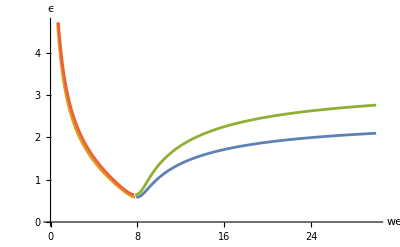

```mathematica
ListLinePlot[{ll,rr,ll0,rr0},AxesLabel->{"we","ϵ"}]
```

```mathematica
ll0=Table[{we,epwe1[we]},{we,0.1,30,0.1}];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
rr0=Table[{we,epwe2[we]},{we,0.1,30,0.1}];
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

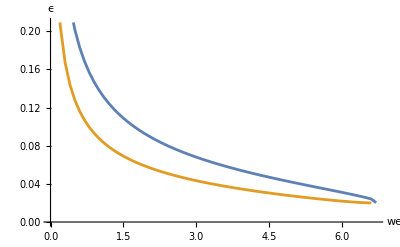

```mathematica
ListLinePlot[{ll,rr},AxesLabel->{"we","ϵ"}]
```

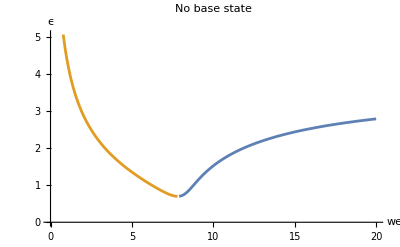

```mathematica
ListLinePlot[{lls,rrs},AxesLabel->{"we","ϵ"},PlotLabel->"No base state"]
```

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
mu1
```

0.71

-Graphics-

```mathematica
zetak
```

zetak

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]
```

```mathematica
Cos[9Pi/8]//N
```

-0.92388

```mathematica
Cos[7Pi/8]//N
```

-0.92388

```mathematica
k212fun=
```

```mathematica
k212fun=Integrate[TrigReduce[(D[eta1,θ]*D[phi12,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi12,φ])+D[eta2,θ]*D[phi11,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi11,φ])+eta1(D[phi11,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi11,r,φ])-2*D[phi11,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi11,φ]*D[eta1,φ]))-eta2*D[phi11,r,r]-eta1*D[phi12,r,r]-eta1^2/2*D[phi11,r,r,r])-(D[eta1,θ]*D[phi22,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi22,φ])+D[eta2,θ]*D[phi21,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi21,φ])+eta1(D[phi21,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi21,r,φ])-2*D[phi21,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi21,φ]*D[eta1,φ]))-eta2*D[phi21,r,r]-eta1*D[phi22,r,r]-eta1^2/2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.426308 b020^2 b021t+0.568411 b021^2 b021t+0.434059 b021t b030^2-0.11264 b021t b120-0.11264 b020t b121+0.204081 b030t b121+b020 (0.142103 b020t b021+0.643654 b021t b030+0.193096 b021 b030t-0.11264 b121t-0.11264 k121-0.135168 l121)+0.116618 b030 l121+b021 (0.430442 b030 b030t-0.11264 b120t+0.204081 b130t-0.11264 k120+0.204081 k130-0.135168 l120+0.204081 l130)

```mathematica
phii2t
```

1/8 (b120tt+k120t) √(5/π) r^2 (-1+3 Cos[θ]^2)+1/12 (b130tt+k130t) √(7/π) r^3 (-3 Cos[θ]+5 Cos[θ]^3)-1/4 (b121tt+k121t) √(15/π) r^2 Cos[θ] Cos[φ] Sin[θ]

```mathematica
phi22
```

-((b120t+k120) √(5/π) (-1+3 Cos[θ]^2))/(12 r^3)-((b130t+k130) √(7/π) (-3 Cos[θ]+5 Cos[θ]^3))/(16 r^4)+((b121t+k121) √(5/(3 π)) Cos[θ] Cos[φ] Sin[θ])/(2 r^3)

```mathematica
n212fun=Integrate[TrigReduce[eta1*(D[phi12t,r]-D[phi22t,r])+eta2*(D[phi11t,r]-D[phi21t,r])+eta1^2/2*(D[phi11t,r,r]-D[phi21t,r,r])+(D[phi11*r]*D[phi12,r]-D[phi21*r]*D[phi22,r])+(D[phi11,θ]*D[phi12,θ]-D[phi21,θ]*D[phi22,θ])+1/Sin[θ]^2*(D[phi11,φ]*D[phi12,φ]-D[phi21,φ]*D[phi22,φ])+eta1*(D[phi11,r]*D[phi11,r,r]-D[phi21,r]*D[phi21,r,r])+eta1*(D[phi11,θ]*D[phi11,r,θ]-D[phi21,θ]*D[phi21,r,θ]+1/Sin[θ]^2*D[phi11,φ]*D[phi11,r,φ]-1/Sin[θ]^2*D[phi21,φ]*D[phi21,r,φ]-D[phi11,θ]^2+D[phi21,θ]^2-1/Sin[θ]^2*D[phi11,φ]+1/Sin[θ]^2*D[phi21,φ])-2/wer*(eta1*((1-2-2^2)*b120*realkl[2,0]+(1-2-2^2)*b121*realkl[2,1]+(1-3-3^2)*b130*realkl[3,0])+eta2*((1-2-2^2)*b020*realkl[2,0]+(1-2-2^2)*b021*realkl[2,1]+(1-3-3^2)*b031*realkl[3,0]))]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.0710513 b020^2 b021tt+0.213154 b021^2 b021tt+0.0306502 b020t b021t b030+0.0874146 b021tt b030^2+0.35629 b021t b030 b030t+0.0563199 b021t b120t+0.0563199 b020t b121t-0.0631679 b030t b121t-0.0777451 b021t b130t+0.0563199 b021t k120+0.0563199 b020t k121-0.0631679 b030t k121-0.0777451 b021t k130+0.0145772 b030t l121+b020 (0.165786 b020t b021t+0.0919505 b021tt b030+0.151718 b021t b030t-0.0450559 l121t)+0.0583088 b030 l121t+0.00971813 b021t l130+(0.901119 b020 b121)/wer-(0.583088 b030 b121)/wer-(1.28279 b031 b121)/wer+1/wer b021 (0.901119 b120-1.86588 b130+(0.37894 b020t^2+0.142103 b020 b020tt+0.553608 b021t^2+0.0919505 b020tt b030+0.634459 b020t b030t+0.523282 b030t^2+0.128731 b020 b030tt+0.244761 b030 b030tt-0.0450559 l120t+0.0583088 l130t) wer)

```mathematica
l212fun=Integrate[TrigReduce[eta1*D[phi12,r,r]+eta2*D[phi11,r,r]+1/2*eta1^2*D[phi11,r,r,r]-(eta1*D[phi22,r,r]+eta2*D[phi21,r,r]+1/2*eta1^2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.284205 b020^2 b021t-0.852616 b021^2 b021t-0.349659 b021t b030^2+0.22528 b021t b120+0.22528 b020t b121-0.408162 b030t b121-0.291544 b030 b121t-0.291544 b021t b130-0.291544 b030 k121+b020 (-0.568411 b020t b021-0.367802 b021t b030-0.514923 b021 b030t+0.22528 b121t+0.22528 k121+0.180224 l121)-0.233235 b030 l121+b021 (-0.367802 b020t b030-0.979044 b030 b030t+0.22528 b120t-0.408162 b130t+0.22528 k120-0.408162 k130+0.180224 l120-0.291544 l130)

```mathematica
v31term=eta1*D[phi2t,r]+eta2*D[phi1t,r]+D[phi1*r]*D[phi2,r]+D[phi1,θ]*D[phi2,θ]+1/Sin[θ]^2*D[phi1,φ]*D[phi2,φ](*+2/wer*(eta1*((1-2-2^2)*b120*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b131*realkl[3,1]+(1-4-4^2)*b140*SphericalHarmonicY[4,0,θ,φ])+eta2*((1-2-2^2)*b020*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b031*realkl[3,1]+(1-4-4^2)*b040*SphericalHarmonicY[4,0,θ,φ]))*);
```

```mathematica
Clear[k120f]
```

```mathematica
k201f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.004703 Cos[2 t]-0.00910368 c0 Cos[2 t]+0.111069 d0 Cos[2 t]+0.135168 c0 d0 Cos[2 t]-0.120336 Sin[2 t]-0.111069 c0 Sin[2 t]-0.0675839 c0^2 Sin[2 t]-0.00910368 d0 Sin[2 t]+0.0675839 d0^2 Sin[2 t]

```mathematica
b020
```

1.23256 Cos[t]+c0 Cos[t]-0.101026 Sin[t]+d0 Sin[t]

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2]
```

```mathematica
k201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k120ff=0.09011187578643427 b020 b020t+0.045055937893217136 b021 b021t+0.168208834801344 b030 b030t;
k1klnow=k120ff//TrigReduce//Chop)
```

```mathematica
k211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k121ff=0.04505593789321714 (b020t b021+b020 b021t);
k1klnow=k121ff//TrigReduce//Chop)
```

```mathematica
Clear[k121f]
```

```mathematica
k301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,k301ff,k1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k301ff=0.084104417400672 b020t b030-0.168208834801344 b020 b030t;
k1klnow=k301ff//TrigReduce//Chop)
```

```mathematica
Clear[k130f]
```

```mathematica
n201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n120ff=1/wer(1.8022375157286856 b020^2+0.9011187578643428 b021^2+3.700594365629568 b030^2+0.037546614911014284 b020t^2 wer+0.018773307455507142 b021t^2 wer+0.036795682612794 b030t^2 wer);
n1klnow=n120ff//TrigReduce//Chop)
```

```mathematica
Clear[n120f]
```

```mathematica
n211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n121ff=-0.03754661491101429 b020t b021t+(1.8022375157286858 b020 b021)/wer;
n1klnow=n121ff//TrigReduce//Chop)
```

```mathematica
n301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,n130ff,n1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n130ff=0.042052208700336 b020t b030t+(5.382682713643008 b020 b030)/wer;
n1klnow=n130ff//TrigReduce//Chop)
```

```mathematica
Clear[n130f]
```

```mathematica
l201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l120ff=0.9011187578643428 b020 b020t+0.4505593789321714 b021 b021t+1.177461843609408 b030 b030t;
l1klnow=l120ff//TrigReduce//Chop)
```

```mathematica
l211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.4505593789321715 (b020t b021+b020 b021t);
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
l301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.8410441740067199 b020t b030+1.177461843609408 b020 b030t;
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
Integrate[eta1*(a1*realkl[2,0]+a3*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}]
```

(5 (232 a1 b020+259 a3 b030) √(5 π))/4096

```mathematica
nm0[k_]:=√((2k+1)/(4*Pi));
```

```mathematica
n201f[0,0,1,0,0,2]
```

64.6106-0.355257 c0+0.1408 c0^2+0.1408 d0^2+50.7729 Cos[2 t]-0.213154 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]-0.213154 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t]

```mathematica
t201=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}];
```

```mathematica
b201[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,f44,f55,Δk,k,eta1,b020,b021,b030,forcing201];k=2;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f44=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f55=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)f4=f44;f5=f55;

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
forcing201
```

0.+0.195146 Cos[2 t]+0.208392 c0 Cos[2 t]+0.135168 c0^2 Cos[2 t]-0.135168 d0^2 Cos[2 t]-0.000513647 Sin[t] (14 √35 (0.-0.666243 Cos[t])+75 (0.+1.1563 Cos[t]+c0 Cos[t]+d0 Sin[t]))+0.208392 d0 Sin[2 t]+0.270336 c0 d0 Sin[2 t]-0.332226 (-1.72746 Cos[2 t]-2.08392 c0 Cos[2 t]-1.35168 c0^2 Cos[2 t]+1.35168 d0^2 Cos[2 t]-2.08392 d0 Sin[2 t]-2.70336 c0 d0 Sin[2 t])-1.99336 (0.20211+0.217075 c0+0.1408 c0^2+0.1408 d0^2+0.135577 Cos[2 t]+0.130245 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]+0.130245 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t])

```mathematica
b020
```

1.14703 Cos[t]+c0 Cos[t]-0.103071 Sin[t]+d0 Sin[t]

```mathematica
b201[0.02,0.67,0.5,0.5,0.5,2]
```

-0.397452-0.429241 c0-0.280664 c0^2+0.0193092 d0-0.280664 d0^2+(-0.162486-0.138668 c0^2+c0 (-0.212723+0.0104421 d0)-0.0174917 d0+0.138668 d0^2) Cos[2 t]+(0.0125894+0.0174917 c0-0.00522106 c0^2-0.212723 d0-0.277337 c0 d0+0.00522106 d0^2) Sin[2 t]

```mathematica
b301[0,0.67,0.5,0,0,2]
```

0.108143+0.093525 c0-0.00610663 d0+(0.505873+0.805274 c0+0.318067 c0^2+0.0301327 d0-0.318067 d0^2) Cos[2 t]+(-0.0178752-0.0301327 c0+0.805274 d0+0.636134 c0 d0) Sin[2 t]

```mathematica
b030
```

0.-0.666243 Cos[t]

```mathematica
b211[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing211];k=2;l=1;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing301];k=3;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing301=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing301,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing301*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing301*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b301sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[0.026,2,1,1,1,2]
```

0.0872234+0.135277 c0-0.166881 d0+(0.276356-0.326047 c0-0.900938 d0) Cos[2 t]+(1.63569+0.900938 c0-0.326047 d0) Sin[2 t]

```mathematica
t2kl[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
b120=b201[oh,ρ1,ρ2,μ1,μ2,2,0,kr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,2,1,kr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,3,0,kr];
eta2=b120*realkl[2,0]+(b121)*realkl[2,1]+b130*realkl[3,0];
tkl1=Integrate[eta2*(nm0[2]*realkl[2,0]+nm0[3]*realkl[3,0])*realkl[k,l],{θ,0,Pi},{φ,0,2 Pi}]//TrigReduce//Chop)
```

```mathematica
k212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,k212ff,k2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];

k212ff=0.42630788328186253 b020^2 b021t+0.5684105110424833 b021^2 b021t+0.43405893570516907 b021t b030^2-0.11263984473304287 b021t b120-0.11263984473304287 b020t b121+0.20408080688521937 b030t b121+b020 (0.14210262776062083 b020t b021+0.6436536512152659 b021t b030+0.1930960953645798 b021 b030t-0.11263984473304288 b121t-0.11263984473304288 k121-0.13516781367965144 l121)+0.11661760393441106 b030 l121+b021 (0.43044177790762606 b030 b030t-0.11263984473304287 b120t+0.20408080688521937 b130t-0.11263984473304287 k120+0.20408080688521937 k130-0.13516781367965144 l120+0.20408080688521937 l130);
k2klnow=k212ff//TrigReduce//Chop)
```

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.0877897 c0 Cos[t]-0.0559945 c0^2 Cos[t]+0.000519548 c0^3 Cos[t]+0.15 d0 Cos[t]+0.295317 c0 d0 Cos[t]+0.256107 c0^2 d0 Cos[t]-0.093676 d0^2 Cos[t]+0.000519548 c0 d0^2 Cos[t]+0.256107 d0^3 Cos[t]-0.104832 c0 Cos[3 t]-0.113301 c0^2 Cos[3 t]+0.00155864 c0^3 Cos[3 t]+0.0867123 d0 Cos[3 t]+0.222335 c0 d0 Cos[3 t]+0.70778 c0^2 d0 Cos[3 t]+0.113301 d0^2 Cos[3 t]-0.00467593 c0 d0^2 Cos[3 t]-0.235927 d0^3 Cos[3 t]-0.141883 c0 Sin[t]-0.154999 c0^2 Sin[t]-0.256107 c0^3 Sin[t]+0.0622896 d0 Sin[t]+0.0376815 c0 d0 Sin[t]+0.000519548 c0^2 d0 Sin[t]+0.140319 d0^2 Sin[t]-0.256107 c0 d0^2 Sin[t]+0.000519548 d0^3 Sin[t]-0.0867123 c0 Sin[3 t]-0.111168 c0^2 Sin[3 t]-0.235927 c0^3 Sin[3 t]-0.104832 d0 Sin[3 t]-0.226602 c0 d0 Sin[3 t]+0.00467593 c0^2 d0 Sin[3 t]+0.111168 d0^2 Sin[3 t]+0.70778 c0 d0^2 Sin[3 t]-0.00155864 d0^3 Sin[3 t]

```mathematica
n212f[0.02,0.7,0.5,0.5,0.5,2]
```

0.141527 c0 Cos[t]+0.103311 c0^2 Cos[t]-0.0388695 c0^3 Cos[t]+0.0338048 d0 Cos[t]-0.0360173 c0 d0 Cos[t]+0.000865913 c0^2 d0 Cos[t]+0.0460325 d0^2 Cos[t]-0.0388695 c0 d0^2 Cos[t]+0.000865913 d0^3 Cos[t]-0.0259412 c0 Cos[3 t]-0.0668027 c0^2 Cos[3 t]-0.329783 c0^3 Cos[3 t]-0.0078983 d0 Cos[3 t]-0.0959533 c0 d0 Cos[3 t]-0.000519548 c0^2 d0 Cos[3 t]+0.0668027 d0^2 Cos[3 t]+0.989348 c0 d0^2 Cos[3 t]+0.000173183 d0^3 Cos[3 t]+0.0042258 c0 Cos[t] k130f[0.02,0.7,0.5,0.5,0.5,2]+0.0534873 c0 Sin[t]+0.0694006 c0^2 Sin[t]-0.000865913 c0^3 Sin[t]-0.0514432 d0 Sin[t]+0.0572783 c0 d0 Sin[t]-0.0388695 c0^2 d0 Sin[t]+0.0333833 d0^2 Sin[t]-0.000865913 c0 d0^2 Sin[t]-0.0388695 d0^3 Sin[t]+0.0042258 d0 k130f[0.02,0.7,0.5,0.5,0.5,2] Sin[t]+0.0078983 c0 Sin[3 t]+0.0479767 c0^2 Sin[3 t]+0.000173183 c0^3 Sin[3 t]-0.0259412 d0 Sin[3 t]-0.133605 c0 d0 Sin[3 t]-0.989348 c0^2 d0 Sin[3 t]-0.0479767 d0^2 Sin[3 t]-0.000519548 c0 d0^2 Sin[3 t]+0.329783 d0^3 Sin[3 t]

```mathematica
n212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,n212ff,n2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];


n212ff=0.07105131388031043 b020^2 b021tt+0.21315394164093127 b021^2 b021tt+0.030650173867393618 b020t b021t b030+0.08741464677395767 b021tt b030^2+0.356290043057993 b021t b030 b030t+0.05631992236652144 b021t b120t+0.05631992236652144 b020t b121t-0.063167868797806 b030t b121t-0.07774506928960738 b021t b130t+0.05631992236652144 b021t k120+0.05631992236652144 b020t k121-0.063167868797806 b030t k121-0.07774506928960738 b021t k130+0.014577200491801383 b030t l121+b020 (0.16578639905405768 b020t b021t+0.09195052160218087 b021tt b030+0.1517183606435984 b021t b030t-0.04505593789321715 l121t)+0.058308801967205545 b030 l121t+0.009718133661200922 b021t l130+(0.9011187578643429 b020 b121)/wer-(0.5830880196720554 b030 b121)/wer+1/wer b021 (0.9011187578643429 b120-1.865881662950577 b130+(0.37894034069498894 b020t^2+0.14210262776062085 b020 b020tt+0.5536081539840855 b021t^2+0.09195052160218087 b020tt b030+0.634458599055048 b020t b030t+0.5232821613778984 b030t^2+0.1287307302430532 b020 b030tt+0.2447610109670815 b030 b030tt-0.04505593789321714 l120t+0.05830880196720553 l130t) wer);
n2klnow=n212ff//TrigReduce//Chop)
```

```mathematica
l212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,l212ff,l2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];



l212ff=-0.2842052555212417 b020^2 b021t-0.8526157665637251 b021^2 b021t-0.3496585870958307 b021t b030^2+0.22527968946608573 b021t b120+0.22527968946608573 b020t b121-0.40816161377043875 b030t b121-0.2915440098360277 b030 b121t-0.2915440098360277 b021t b130-0.2915440098360277 b030 k121+b020 (-0.5684105110424834 b020t b021-0.36780208640872347 b021t b030-0.5149229209722128 b021 b030t+0.22527968946608576 b121t+0.22527968946608576 k121+0.18022375157286857 l121)-0.23323520786882213 b030 l121+b021 (-0.36780208640872347 b020t b030-0.979044043868326 b030 b030t+0.22527968946608573 b120t-0.40816161377043875 b130t+0.22527968946608573 k120-0.40816161377043875 k130+0.18022375157286857 l120-0.2915440098360277 l130);
l2klnow=l212ff//TrigReduce//Chop)
```

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2,1]
```

0.-9.76696 Sin[t]

```mathematica
b020
```

0.-9.76696 Sin[t]

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2,1]
```

0.139615 c0 Cos[t]+2.09011 d0 Cos[t]-9.86024 c0 Cos[1. t]+0.000109138 c0^3 Cos[1. t]+298.137 d0 Cos[1. t]+0.134504 c0^2 d0 Cos[1. t]+0.000109138 c0 d0^2 Cos[1. t]+0.134504 d0^3 Cos[1. t]+0.0539565 c0 Cos[3 t]+1.27763 d0 Cos[3 t]-10.4138 c0 Cos[3. t]+0.000327414 c0^3 Cos[3. t]-297.275 d0 Cos[3. t]+0.40679 c0^2 d0 Cos[3. t]-0.000982242 c0 d0^2 Cos[3. t]-0.135597 d0^3 Cos[3. t]-3.30591 c0 Sin[t]+0.139615 d0 Sin[t]-357.469 c0 Sin[1. t]-0.134504 c0^3 Sin[1. t]+9.86024 d0 Sin[1. t]+0.000109138 c0^2 d0 Sin[1. t]-0.134504 c0 d0^2 Sin[1. t]+0.000109138 d0^3 Sin[1. t]-1.27763 c0 Sin[3 t]+0.0539565 d0 Sin[3 t]+297.275 c0 Sin[3. t]-0.135597 c0^3 Sin[3. t]-10.4138 d0 Sin[3. t]+0.000982242 c0^2 d0 Sin[3. t]+0.40679 c0 d0^2 Sin[3. t]-0.000327414 d0^3 Sin[3. t]

```mathematica
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
```

```mathematica
harmonic21[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,tkl1,tkl2,eta1,fk,b211sol];
eta2=(*b120*realkl[2,0]+*)b211sol*realkl[2,1](*+b130*realkl[3,0]*);
tkl2=Integrate[eta2*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/wek;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
zetak=wer/we;
b211sol=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl2=k212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];kkl2t=D[kkl2,t];
nkl2=n212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl2=l212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];lkl2t=D[lkl2,t];
forcing212=(ρ2-ρ1)*fk*tkl2*Sin[t]-kkl2t-2*Δk*kkl2-gk*lkl2t-hk*lkl2-fk*nkl2;//TrigReduce;
fcos=Integrate[(1/Pi)*forcing212*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forcing212*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c0]-Coefficient[fsin,c0*d0^2]*d0^2//FullSimplify//Chop;g2=Coefficient[fsin,d0]-Coefficient[fsin,d0*c0^2]*c0^2//FullSimplify//Chop;g3=Coefficient[fcos,c0]-Coefficient[fcos,c0*d0^2]*d0^2//FullSimplify//Chop;g4=Coefficient[fcos,d0]-Coefficient[fcos,d0*c0^2]*c0^2//FullSimplify//Chop;
α=Coefficient[fcos,c0^3]//Chop;
β=Coefficient[fcos,d0^3]//Chop;

wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/(√wek);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
data={g1,g2,g3,g4,α,β,Δk,wer}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2,1]
```

{13.5044,-844.346,-689.325,22.751,-0.400045,0.00570439,0.0501485,27.907}

```mathematica
(g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4
```

24031.6+(4 (0.100297+13.5044 ϵ^2) (-0.100297+22.751 ϵ^2))/ϵ^4

```mathematica
Solve[24031.60632735587+1/ϵ^4 4 (0.10029701698998988+13.504418503560936 ϵ^2) (-0.10029701698998988+22.75099356674131 ϵ^2)==0,ϵ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ→-0.0345082},{ϵ→0.-0.0365742 ⅈ},{ϵ→0.+0.0365742 ⅈ},{ϵ→0.0345082}}

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
Integrate[realkl[2,1]*realkl[2,1]*realkl[2,1](**realkl[2,1]*)*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[2,0]*realkl[2,1]*realkl[2,1]*realkl[2,1]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[3,1]*realkl[3,1]*(*realkl[3,1]**)realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]
```

0

```mathematica
expr
```

(-1/4 √(15/π) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t])-1/2 √(3/π) (-0.594135 Cos[t]+0.00569606 Sin[t]) Sin[θ]-24.9054 Cos[θ] Sin[t] Sin[θ]+1/12 √(7/π) (0.363423 Cos[t]+0.0122865 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ])) (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])+49.8108 Cos[t] Cos[θ] Sin[θ]-1/2 √(3/π) (-0.00569606 Cos[t]-0.594135 Sin[t]) Sin[θ]+1/4 √(7/π) (-0.0122865 Cos[t]+0.363423 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))-(-8.30181 Cos[t] (-1+3 Cos[θ]^2)+1/2 √(3/π) Cos[θ] (-0.00569606 Cos[t]-0.594135 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.0122865 Cos[t]+0.363423 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (1/2 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (0.363423 Cos[t]+0.0122865 Sin[t])-1/4 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) Sin[2 θ])+1/(32 π)15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]^2 Sin[φ]^2

## Variable contact area forcing

```mathematica
Clear[pkc]
```

```mathematica
Series[Cos[a],{a,0,2}]
```

1-a^2/2+O[a]^3

```mathematica
LegendreP[3,Cos[Pi/4]]//N
```

-0.176777

```mathematica
LegendreP[3,1-Pi^2/16]//N
```

-0.434105

```mathematica
Series[LegendreP[k,1-e],{e,0,2}]//FullSimplify
```

1-1/2 (k (1+k)) e+1/16 (-1+k) k (1+k) (2+k) e^2+O[e]^3

```mathematica
pkcapp[k_,es_]:=1-es/2 k(k+1)+es^2/16*k(k^2-1)(k+2);
```

```mathematica
1-es/2 k(k+1)+es^2/16*k(k^2-1)(k+2)/.es->1-Cos[a]
```

1-1/2 k (1+k) (1-Cos[a])+1/16 k (2+k) (-1+k^2) (1-Cos[a])^2

```mathematica
pkcfull[k_,α_]:=LegendreP[k,Cos[α]]
```

```mathematica
pkcfull[2,Pi/4]//N
```

0.25

```mathematica
pkcapp[2,1-Cos[Pi/4]]//N
```

0.25

```mathematica
LegendreP[k,1]
```

1

```mathematica
Integrate[LegendreP[2,Cos[t]]*Sin[t]*Cos[t],{t,0,Pi/4}]
```

5/32

```mathematica
qkfull=1/(2k+1)*(((k+1)/(2k+3)*(pkcfull[k,a]-pkcfull[k+2,a]))+k/(2k-1)*(pkcfull[k-2,a]-pkcfull[k,a]))/.{k->2,a->Pi/4}
```

5/32

```mathematica
qkapp=1/(2k+1)*(((k+1)/(2k+3)*(pkcapp[k,ep]-pkcapp[k+2,ep]))+k/(2k-1)*(pkcapp[k-2,ep]-pkcapp[k,ep]))/.{k->2,ep->0.2}
```

0.12

```mathematica
qkapp=1/(2k+1)*(((k+1)/(2k+3)*(pkcapp[k,ep]-pkcapp[k+2,ep]))+k/(2k-1)*(pkcapp[k-2,ep]-pkcapp[k,ep]))/.{k->3,ep->0.2}
```

0.06

```mathematica
1/(2k+1)*(((k+1)/(2k+3)*(pkcapp[k,ep]-pkcapp[k+2,ep]))+k/(2k-1)*(pkcapp[k-2,ep]-pkcapp[k,ep]))//FullSimplify
```

ep-1/4 ep^2 (2+k+k^2)

```mathematica
(1-Cos[2*omg*t])^2//TrigReduce
```

1/2 (3-4 Cos[2 omg t]+Cos[4 omg t])

```mathematica
Integrate[LegendreP[2,Cos[t]]*Sin[t]*Cos[t],{t,0,Pi/10}]//N
```

0.0443263

```mathematica
qkk=1/(2k+1)*(((k+1)/(2k+3)*(pkc[k]-pkc[k+2]))+k/(2k-1)*(pkc[k-2]-pkc[k]))//FullSimplify
```

es-1/4 es^2 (2+k+k^2)

```mathematica
ArcCos[0.5]//N
```

1.0472

```mathematica
Integrate[LegendreP[2,ArcCos[0.5]]*Sin[θ]*Cos[θ],{θ,0,ArcCos[0.5]}]
```

0.42935

```mathematica
qkk/.{k->2,es->0.5}
```

0.

```mathematica
Integrate
```

```mathematica
DSolve[bkl1''[t]+2*deltak*bkl1'[t]+zetak^2*bkl1[t]==rhoj*(1-Cos[2t])*(-gg+Sin[t]),bkl1[t],t]//FullSimplify
```

{{bkl1[t]→-(gg rhoj)/zetak^2+ⅇ^(-t (deltak+√(deltak^2-zetak^2))) (C[1]+ⅇ^(2 t √(deltak^2-zetak^2)) C[2])+1/2 rhoj (-(6 deltak Cos[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(2 gg (-4+zetak^2) Cos[2 t])/(16 deltak^2+(-4+zetak^2)^2)+(6 deltak Cos[3 t])/(36 deltak^2+(-9+zetak^2)^2)+(3 (-1+zetak^2) Sin[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(8 deltak gg Sin[2 t])/(16 deltak^2+(-4+zetak^2)^2)-((-9+zetak^2) Sin[3 t])/(36 deltak^2+(-9+zetak^2)^2))}}

```mathematica
fnnm[oh_,bo_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]:=(
delta=oh/we;gg=bo/we;
rhoj=ρ1-ρ2;
fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
deltak=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we));

plf=-(gg rhoj)/zetak^2+1/2 rhoj (-(6 deltak Cos[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(2 gg (-4+zetak^2) Cos[2 t])/(16 deltak^2+(-4+zetak^2)^2)+(6 deltak Cos[3 t])/(36 deltak^2+(-9+zetak^2)^2)+(3 (-1+zetak^2) Sin[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(8 deltak gg Sin[2 t])/(16 deltak^2+(-4+zetak^2)^2)-((-9+zetak^2) Sin[3 t])/(36 deltak^2+(-9+zetak^2)^2)))
```

```mathematica
l20=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,2,0]
```

-0.001716+0.36 (-0.346749 Cos[t]-0.000774935 Cos[2 t]+0.000947076 Cos[3 t]-6.79182 Sin[t]+0.0000101321 Sin[2 t]+0.118468 Sin[3 t])

```mathematica
l30=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,3,0]
```

-0.0004632+0.36 (-0.133104 Cos[t]-0.00137963 Cos[2 t]+0.00319627 Cos[3 t]+2.79075 Sin[t]+0.0000732299 Sin[2 t]+0.144282 Sin[3 t])

```mathematica
l40=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,4,0]
```

-0.0001944+0.36 (-0.0176518 Cos[t]+0.00273837 Cos[2 t]+0.0165288 Cos[3 t]+0.761346 Sin[t]+0.000532974 Sin[2 t]+0.245086 Sin[3 t])

```mathematica
l50=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,5,0]
```

-0.000100457+0.36 (-0.0058558 Cos[t]+0.000478667 Cos[2 t]+0.869165 Cos[3 t]+0.35052 Sin[t]+0.0000246284 Sin[2 t]-1.12756 Sin[3 t])

```mathematica
l60=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,6,0]
```

-0.0000588+0.36 (-0.00263103 Cos[t]+0.000216094 Cos[2 t]+0.0114344 Cos[3 t]+0.195704 Sin[t]+7.22441×10^-6 Sin[2 t]-0.135526 Sin[3 t])

```mathematica
l70=fnnm[0.043,0.02,15,0.86,0.14,0.71,0.29,7,0]
```

-0.0000374286+0.36 (-0.00138548 Cos[t]+0.000123095 Cos[2 t]+0.00302951 Cos[3 t]+0.121694 Sin[t]+3.19129×10^-6 Sin[2 t]-0.059911 Sin[3 t])

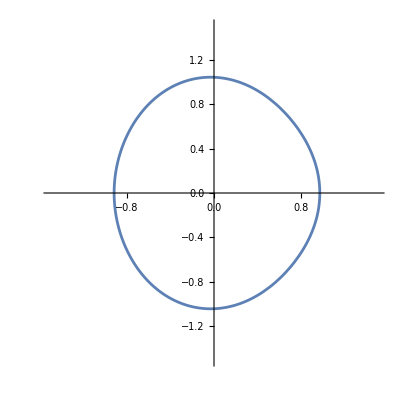

```mathematica
ti=0.2;Rotate[PolarPlot[1+0.2*((l20/.t->ti)*SphericalHarmonicY[2,0,θ,0]+(l30/.t->ti)*SphericalHarmonicY[3,0,θ,0]+(l40/.t->ti)*SphericalHarmonicY[4,0,θ,0]),{θ,0,2Pi},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],-Pi/2]
```

```mathematica
1-0.1*Sin[t]
```

```mathematica
frames=Table[Rotate[PolarPlot[1+0.1*((l20/. t->ti)*SphericalHarmonicY[2,0,θ,0]+(l30/. t->ti)*SphericalHarmonicY[3,0,θ,0]+(l40/. t->ti)*SphericalHarmonicY[4,0,θ,0]+(l50/. t->ti)*SphericalHarmonicY[5,0,θ,0]+(l60/. t->ti)*SphericalHarmonicY[6,0,θ,0]+(l70/. t->ti)*SphericalHarmonicY[7,0,θ,0]),{θ,0,2 Pi},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->StringForm["t = ``",NumberForm[ti,{3,2}]]],-Pi/2],{ti,0,2 Pi-2 Pi/20,2 Pi/20}];

ListAnimate[frames]
```

```mathematica
framesplate=Table[Rotate[Show[PolarPlot[1+0.1*((l20/. t->ti)*SphericalHarmonicY[2,0,θ,0]+(l30/. t->ti)*SphericalHarmonicY[3,0,θ,0]+(l40/. t->ti)*SphericalHarmonicY[4,0,θ,0]+(l50/. t->ti)*SphericalHarmonicY[5,0,θ,0]+(l60/. t->ti)*SphericalHarmonicY[6,0,θ,0]+(l70/. t->ti)*SphericalHarmonicY[7,0,θ,0]),{θ,0,2 Pi},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLabel->StringForm["t = ``",NumberForm[ti,{3,2}]]],Graphics[{Red,Dashed,Line[{{1-0.1*Sin[ti],-1.5},{1-0.1*Sin[ti],1.5}}]}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}],-Pi/2],{ti,0,2 Pi-2 Pi/20,2 Pi/20}];

ListAnimate[framesplate]
```

PolarPlot::nonopt: Options expected (instead of Null) beyond position 2 in PolarPlot[1+0.1 ((l20/.t→ti) SphericalHarmonicY[2,0,θ,0]+(l30/.t→ti) SphericalHarmonicY[3,0,θ,0]+(l40/.t→ti) SphericalHarmonicY[4,0,θ,0]+(l50/.t→ti) SphericalHarmonicY[5,0,θ,0]+(l60/.t→ti) SphericalHarmonicY[6,0,θ,0]+(l70/.t→ti) SphericalHarmonicY[7,0,θ,0]),{θ,0,2 π},«9»→{«1»},Null,PlotLabel→t = ti]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[PolarPlot[«1»],,PlotRange→{{-1.5,1.5},{-1.5,1.5}}].

PolarPlot::nonopt: Options expected (instead of Null) beyond position 2 in PolarPlot[1+0.1 ((l20/.t→ti) SphericalHarmonicY[2,0,θ,0]+(l30/.t→ti) SphericalHarmonicY[3,0,θ,0]+(l40/.t→ti) SphericalHarmonicY[4,0,θ,0]+(l50/.t→ti) SphericalHarmonicY[5,0,θ,0]+(l60/.t→ti) SphericalHarmonicY[6,0,θ,0]+(l70/.t→ti) SphericalHarmonicY[7,0,θ,0]),{θ,0,2 π},«9»→{«1»},Null,PlotLabel→t = ti]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in Show[PolarPlot[«1»],,PlotRange→{{-1.5,1.5},{-1.5,1.5}}].

PolarPlot::nonopt: Options expected (instead of Null) beyond position 2 in PolarPlot[1+0.1 ((l20/.t→ti) SphericalHarmonicY[2,0,θ,0]+(l30/.t→ti) SphericalHarmonicY[3,0,θ,0]+(l40/.t→ti) SphericalHarmonicY[4,0,θ,0]+(l50/.t→ti) SphericalHarmonicY[5,0,θ,0]+(l60/.t→ti) SphericalHarmonicY[6,0,θ,0]+(l70/.t→ti) SphericalHarmonicY[7,0,θ,0]),{θ,0,2 π},«9»→{«1»},Null,PlotLabel→t = ti]. An option must be a rule or a list of rules.

General::stop: Further output of PolarPlot::nonopt will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[PolarPlot[«1»],,PlotRange→{{-1.5,1.5},{-1.5,1.5}}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
fnn[oh_,bo_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]:=(
delta=oh/we;gg=bo/we;
rhoj=ρ1-ρ2;
fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
deltak=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we));

plf=-(gg rhoj)/zetak^2+1/2 rhoj (-(6 deltak Cos[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(2 gg (-4+zetak^2) Cos[2 t])/(16 deltak^2+(-4+zetak^2)^2)+(6 deltak Cos[3 t])/(36 deltak^2+(-9+zetak^2)^2)+(3 (-1+zetak^2) Sin[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(8 deltak gg Sin[2 t])/(16 deltak^2+(-4+zetak^2)^2)-((-9+zetak^2) Sin[3 t])/(36 deltak^2+(-9+zetak^2)^2));
bkl1l2norm=(Integrate[(plf)^2,{t,0,2Pi}])^(1/2)/(2Pi)//Chop)
```

```mathematica
Table[{wee,fnn[0.043,0.0,wee,0.86,0.14,0.71,0.29,2,0]}]
```

1.8539

```mathematica
bkl1l2norm=(Integrate[(plf)^2,{t,0,2Pi}])^(1/2)/(2Pi)//Chop
```

9.21261

```mathematica
listk2=Table[fnn[0.043,0.86,0.14,0.71,0.29,2,0,wee],{wee,0.1,30,0.1}];
```

```mathematica
Integrate[realklpt[k,l,t,p]*Sin[t]*Cos[t],{t,0,alph},{p,0,2Pi},Assumptions->alph>0]
```

Integrate[Cos[t] (Piecewise[{{√2 Re[SphericalHarmonicY[k,l,t,p]], l>0}, {SphericalHarmonicY[k,0,t,0], l==0}, {0, True}}]) Sin[t],{t,0,alph},{p,0,2 π},Assumptions→alph>0]

```mathematica
Integrate[SphericalHarmonicY[k,0,t,p]*Sin[t]*Cos[t],{t,0,alph},{p,0,2Pi},Assumptions->alph>0]
```

FunctionDomain::nmet: Unable to find the domain with the available methods.

Integrate[Cos[t] Sin[t] SphericalHarmonicY[k,0,t,p],{t,0,alph},{p,0,2 π},Assumptions→alph>0]

```mathematica
Clear[deltak,zetak,rhoj,q1k]
```

```mathematica
DSolve[bkl1''[t]+2*deltak*bkl1'[t]+zetak^2*bkl1[t]==rhoj*bo(*q1k(1-Cos[2t])*Sin[t]*),bkl1[t],t]//FullSimplify
```

{{bkl1[t]→(bo rhoj)/zetak^2+ⅇ^(-t (deltak+√(deltak^2-zetak^2))) (C[1]+ⅇ^(2 t √(deltak^2-zetak^2)) C[2])}}

```mathematica
qk0[k_,del_]:=1/(2k+1)*(((k+1)*(LegendreP[k+2,Cos[del]]-LegendreP[k,Cos[del]]))/(2k+3)+k/(2k-1)*(LegendreP[k,Cos[del]]-LegendreP[k-2,Cos[del]]))
```

```mathematica
qk0[2,0.5]
```

-0.095113

```mathematica
bkl1fun[0.043,0.02,0.86,0.14,0.71,0.29,2,0,2,1]//Expand
```

-0.0004632-99.5159 Cos[t]-0.000154392 Cos[2 t]+0.000183134 Cos[3 t]-2.03611×10^-12 Sin[t]+1.11703×10^-6 Sin[2 t]+0.0449993 Sin[3 t]

```mathematica
bkl2fun[0.043,0.02,0.86,0.14,0.71,0.29,2,0,2,1]//Expand
```

190.011 Cos[2 t]+5.67771 c21 Cos[2 t]-0.0206204 c21^2 Cos[2 t]-0.377675 d21 Cos[2 t]+0.000680037 c21 d21 Cos[2 t]+0.0206204 d21^2 Cos[2 t]+0.00647811 Cos[3 t]+0.0000178277 c21 Cos[3 t]-6.28489×10^-8 d21 Cos[3 t]+17.5987 Cos[4 t]+0.0540374 c21 Cos[4 t]-0.0678808 d21 Cos[4 t]+6.48353 Cos[t] Sin[t]-0.811696 c21 Cos[t] Sin[t]-0.000680037 c21^2 Cos[t] Sin[t]+12.5539 d21 Cos[t] Sin[t]-0.0824815 c21 d21 Cos[t] Sin[t]+0.000680037 d21^2 Cos[t] Sin[t]+0.000167831 Sin[3 t]+6.28489×10^-8 c21 Sin[3 t]+0.0000178277 d21 Sin[3 t]+20.6733 Sin[4 t]+0.0678808 c21 Sin[4 t]+0.0540374 d21 Sin[4 t]

```mathematica
Clear[f1,f2,f3,f4,f5]
```

```mathematica
DSolve[x''[t]+2*deltakk*x'[t]+zetakk^2*x[t]==f1+f2*Cos[2t]+f3*Sin[2t]+f4*Cos[3t]+f5*Sin[3t]+f6*Cos[4t]+f7*Sin[4t],x[t],t]//FullSimplify
```

{{x[t]→f1/zetakk^2+ⅇ^(-t (deltakk+√(deltakk^2-zetakk^2))) (C[1]+ⅇ^(2 t √(deltakk^2-zetakk^2)) C[2])+((-4 deltakk f3+f2 (-4+zetakk^2)) Cos[2 t])/(16 deltakk^2+(-4+zetakk^2)^2)+((-6 deltakk f5+f4 (-9+zetakk^2)) Cos[3 t])/(36 deltakk^2+(-9+zetakk^2)^2)+((-8 deltakk f7+f6 (-16+zetakk^2)) Cos[4 t])/(64 deltakk^2+(-16+zetakk^2)^2)+((4 deltakk f2+f3 (-4+zetakk^2)) Sin[2 t])/(16 deltakk^2+(-4+zetakk^2)^2)+((6 deltakk f4+f5 (-9+zetakk^2)) Sin[3 t])/(36 deltakk^2+(-9+zetakk^2)^2)+((8 deltakk f6+f7 (-16+zetakk^2)) Sin[4 t])/(64 deltakk^2+(-16+zetakk^2)^2)}}

```mathematica
Clear[Δk,ζk]
```

```mathematica
((-4 deltakk f3+f2 (-4+zetakk^2)) Cos[2 t])/(16 deltakk^2+(-4+zetakk^2)^2)+((-6 deltakk f5+f4 (-9+zetakk^2)) Cos[3 t])/(36 deltakk^2+(-9+zetakk^2)^2)+((-8 deltakk f7+f6 (-16+zetakk^2)) Cos[4 t])/(64 deltakk^2+(-16+zetakk^2)^2)+((4 deltakk f2+f3 (-4+zetakk^2)) Sin[2 t])/(16 deltakk^2+(-4+zetakk^2)^2)+((6 deltakk f4+f5 (-9+zetakk^2)) Sin[3 t])/(36 deltakk^2+(-9+zetakk^2)^2)+((8 deltakk f6+f7 (-16+zetakk^2)) Sin[4 t])/(64 deltakk^2+(-16+zetakk^2)^2)/.{deltakk->Δk,zetakk->ζk}//FullSimplify
```

((-4 f3 Δk+f2 (-4+ζk^2)) Cos[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((-6 f5 Δk+f4 (-9+ζk^2)) Cos[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((-8 f7 Δk+f6 (-16+ζk^2)) Cos[4 t])/(64 Δk^2+(-16+ζk^2)^2)+((4 f2 Δk+f3 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((6 f4 Δk+f5 (-9+ζk^2)) Sin[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((8 f6 Δk+f7 (-16+ζk^2)) Sin[4 t])/(64 Δk^2+(-16+ζk^2)^2)

```mathematica
bkl1fun[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/we;gg=bo/we;
rhoj=ρ1-ρ2;
fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
deltak=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
bkl0amp=plf=-(gg rhoj)/zetak^2+1/2 rhoj (-(6 deltak Cos[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(2 gg (-4+zetak^2) Cos[2 t])/(16 deltak^2+(-4+zetak^2)^2)+(6 deltak Cos[3 t])/(36 deltak^2+(-9+zetak^2)^2)+(3 (-1+zetak^2) Sin[t])/(1+4 deltak^2-2 zetak^2+zetak^4)+(8 deltak gg Sin[2 t])/(16 deltak^2+(-4+zetak^2)^2)-((-9+zetak^2) Sin[3 t])/(36 deltak^2+(-9+zetak^2)^2)))(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
fkl1
```

-168.57-0.00201118 c21-0.10689 c21^2-0.0487024 d21-0.10689 d21^2+0.00389565 Cos[t]+0.000125797 c21 Cos[t]+0.0000125831 d21 Cos[t]-36.8659 Cos[2 t]-4.26262 c21 Cos[2 t]+0.0618338 c21^2 Cos[2 t]+0.407576 d21 Cos[2 t]-0.00535628 c21 d21 Cos[2 t]-0.0618338 d21^2 Cos[2 t]-0.053989 Cos[3 t]-0.000526969 c21 Cos[3 t]+0.0000171745 d21 Cos[3 t]-49.895 Cos[4 t]-0.524855 c21 Cos[4 t]+0.15075 d21 Cos[4 t]-0.00155052 Cos[5 t]+0.986729 Cos[6 t]-0.00203477 Sin[t]+0.0000164453 c21 Sin[t]-0.0000297354 d21 Sin[t]-15.4942 Sin[2 t]+0.0573723 c21 Sin[2 t]+0.00267814 c21^2 Sin[2 t]-5.41347 d21 Sin[2 t]+0.123668 c21 d21 Sin[2 t]-0.00267814 d21^2 Sin[2 t]-0.00266288 Sin[3 t]-0.0000171745 c21 Sin[3 t]-0.000526969 d21 Sin[3 t]-7.75354 Sin[4 t]-0.15075 c21 Sin[4 t]-0.524855 d21 Sin[4 t]-0.000930371 Sin[5 t]+1.04627 Sin[6 t]

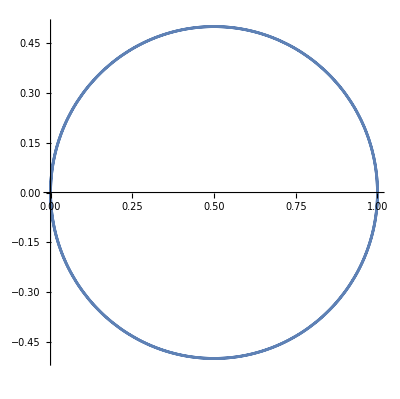

```mathematica
PolarPlot[1Cos[t],{t,0,2Pi}]
```

```mathematica
bkl2fun[oh_,bo_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,f201,wem,We,expr];

expr=kkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

expr=lkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
lkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};


wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);

expr=nkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,We->wem};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;
expr=nkl1fun/.{ohn->oh,bond->bo,rho1->ρ1,rho2->ρ2,mu1->μ1,mu2->μ2,We->wem};
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[k,l,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
nkl1ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};
bkl1sol=bkl1fun[oh,bo,ρ1,ρ2,μ1,μ2,k,l,m,n];

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);We=wem;(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;gg=bo/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k);fk=(k(k+1))/(ρ1(k+1)+ρ2*k);gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;hk=2*delta*μ2*(k+2);
qk2=-1/8(k^2+k+2)*(3-4*Cos[2t]+4*Cos[4t]);
(*compute the forcing terms*)

fkl1=TrigReduce[nk*(-gg+Sin[t])*bkl1sol*(1-Cos[2t])+qk2-D[kkl1ff,t]-2*Δk*kkl1ff-fk*nkl1ff-gk*D[lkl1ff,t]-hk*lkl1ff];

f1=Integrate[(1/(2Pi))*fkl1,{t,-Pi,Pi}];
f2=Integrate[(1/Pi)*fkl1*Cos[2t],{t,-Pi,Pi}];f3=Integrate[(1/Pi)*fkl1*Sin[2t],{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*fkl1*Cos[3t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*fkl1*Sin[3t],{t,-Pi,Pi}];
f6=Integrate[(1/Pi)*fkl1*Cos[4t],{t,-Pi,Pi}];f7=Integrate[(1/Pi)*fkl1*Sin[4t],{t,-Pi,Pi}];

bkl2sol=((-4 f3 Δk+f2 (-4+ζk^2)) Cos[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((-6 f5 Δk+f4 (-9+ζk^2)) Cos[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((-8 f7 Δk+f6 (-16+ζk^2)) Cos[4 t])/(64 Δk^2+(-16+ζk^2)^2)+((4 f2 Δk+f3 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)+((6 f4 Δk+f5 (-9+ζk^2)) Sin[3 t])/(36 Δk^2+(-9+ζk^2)^2)+((8 f6 Δk+f7 (-16+ζk^2)) Sin[4 t])/(64 Δk^2+(-16+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
expr=kkl2fun/.{ohn->0.043,bond->0.02,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29};
(*expr=kkl1fun/.{ohn->0.043,rho1->0.86,rho2->0.14,mu1->0.71,mu2->0.29,alpha->Pi/2};*)
exprsub=Expand[Rationalize[expr,0]]/. {Cos[t]->ct,Sin[t]->st,Cos[2t]->ct2,Sin[2t]->st2,Cos[3t]->ct3,Sin[3t]->st3};
params={c21,d21,ct,st,ct2,st2,ct3,st3};
rules=CoefficientRules[exprsub,params];
integratedRules=ParallelMap[{#[[1]],Integrate[TrigReduce[Expand[#[[2]]]*realklpt[2,1,θ,φ]*Sin[θ]],{θ,0,π},{φ,0,2 π}]}&,rules];
(*Reassemble*)
kkl2ff=Rationalize[FullSimplify[N[Total[Times[Inner[Power,params,#[[1]],Times],#[[2]]]&/@integratedRules]]],0]/. {ct->Cos[t],st->Sin[t],ct2->Cos[2t],st2->Sin[2t],ct3->Cos[3t],st3->Sin[3t]};
```

$Aborted

Inner::incom: Length 8 of dimension 1 in {c21,d21,ct,st,ct2,st2,ct3,st3} is incommensurate with length 6 of dimension 1 in {2,0,1,1,0,0}.

Inner::incom: Length 8 of dimension 1 in {c21,d21,ct,st,ct2,st2,ct3,st3} is incommensurate with length 6 of dimension 1 in {1,1,2,0,0,0}.

Inner::incom: Length 8 of dimension 1 in {c21,d21,ct,st,ct2,st2,ct3,st3} is incommensurate with length 6 of dimension 1 in {1,1,0,2,0,0}.

General::stop: Further output of Inner::incom will be suppressed during this calculation.

```mathematica
rules
```

```mathematica
nkl1fun=chudmar/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ1->Function[{r,θ,φ,t},fi1[r,θ,φ,t]]}
```

(75/56 (-1+3 Cos[θ]^2) Sin[t]+3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (-c31 Cos[t]-d31 Sin[t]) Sin[θ]) (-75/56 (-1+3 Cos[θ]^2) Sin[t]-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ])+1/We(-2 (-75/56 (-1+3 Cos[θ]^2) Sin[t]-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ])^2+2 (-75/56 (-1+3 Cos[θ]^2) Sin[t]-3/32 (3-30 Cos[θ]^2+35 Cos[θ]^4) Sin[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]) (-225/28 Cos[θ]^2 Sin[t]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] Csc[θ] (c31 Cos[t]+d31 Sin[t])-5/2 √(21/(2 π)) Cos[2 θ] Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ]+225/28 Sin[t] Sin[θ]^2+3/32 Sin[t] (60 Cos[θ]^2-140 Cos[θ]^4-60 Sin[θ]^2+420 Cos[θ]^2 Sin[θ]^2)-5/2 √(21/(2 π)) Cos[θ] Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[2 θ]-Cot[θ] (-1/8 √(21/(2 π)) Cos[θ] (3+5 Cos[2 θ]) Cos[φ] (c31 Cos[t]+d31 Sin[t])+225/28 Cos[θ] Sin[t] Sin[θ]-3/32 Sin[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ])+5/4 √(21/(2 π)) Cos[φ] (c31 Cos[t]+d31 Sin[t]) Sin[θ] Sin[2 θ])))+1/2 ((-75/56 Cos[t] (-1+3 Cos[θ]^2)-3/32 Cos[t] (3-30 Cos[θ]^2+35 Cos[θ]^4)-1/8 √(21/(2 π)) (3+5 Cos[2 θ]) Cos[φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ])^2+(1/32 √(21/(2 π)) Cos[θ] (3+5 Cos[2 θ]) Cos[φ] (d31 Cos[t]-c31 Sin[t])-75/28 Cos[t] Cos[θ] Sin[θ]+3/160 Cos[t] (60 Cos[θ] Sin[θ]-140 Cos[θ]^3 Sin[θ])-5/16 √(21/(2 π)) Cos[φ] (d31 Cos[t]-c31 Sin[t]) Sin[θ] Sin[2 θ])^2+(21 (3+5 Cos[2 θ])^2 (d31 Cos[t]-c31 Sin[t])^2 Sin[φ]^2)/(2048 π))